# Programación Gráfica

César Guerra
cesarg@wolfram.com

## Comandos Gráficos

### Gráficos en Dos Dimensiones

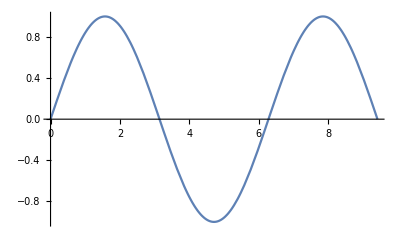

```mathematica
Plot[Sin[x],{x,0,3π}]
```

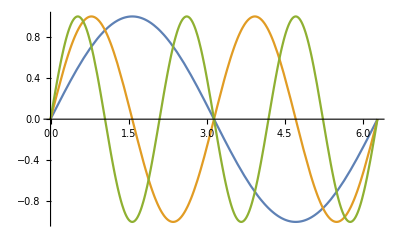

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 π}]
```

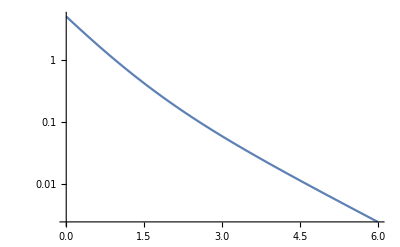

```mathematica
LogPlot[Exp[-x]+4 Exp[-2x],{x,0,6}]
```

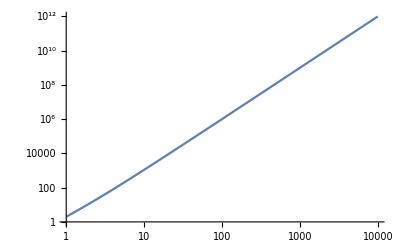

```mathematica
LogLogPlot[x^2+x^3,{x,1,10000}]
```

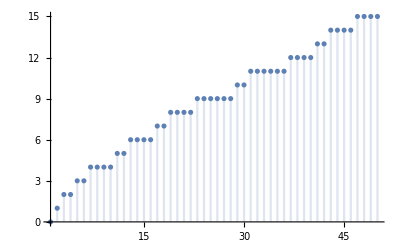

```mathematica
DiscretePlot[PrimePi[k],{k,1,50}]
```

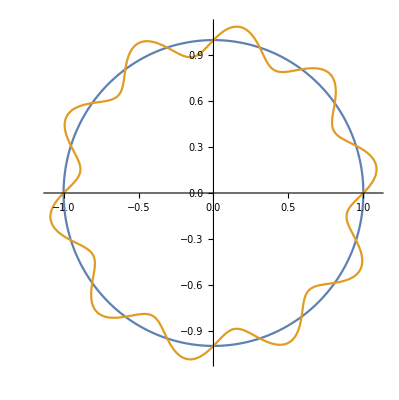

```mathematica
PolarPlot[{1,1+1/10 Sin[10θ]},{θ,0,2Pi}]
```



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π}]
```

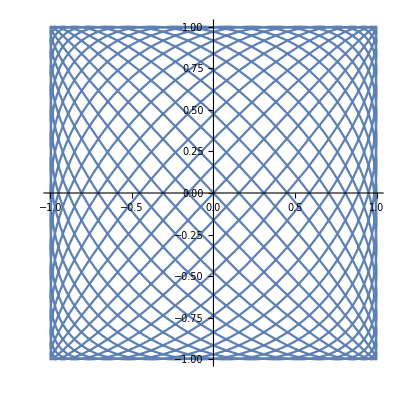

```mathematica
ParametricPlot[{Cos[19t],Sin[20t]},{t,0,2π}]
```

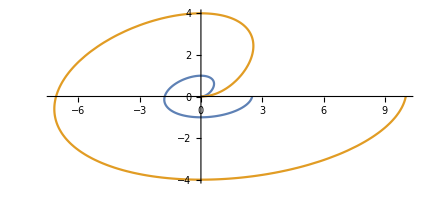

```mathematica
ParametricPlot[{{ Sqrt[t]Cos[t], Sin[t]},4{ Sqrt[t]Cos[t], Sin[t]}},{t,0,2π}]
```

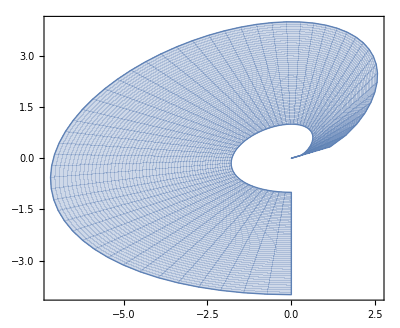

```mathematica
ParametricPlot[r^2{ Sqrt[t]Cos[t], Sin[t]},{t,0,3Pi/2},{r,1,2}]
```

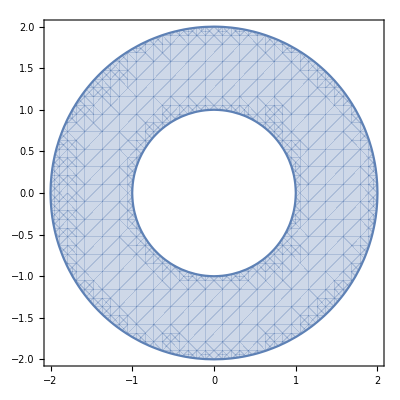

```mathematica
RegionPlot[1<x^2+y^2<4,{x,-2,2},{y,-2,2}]
```

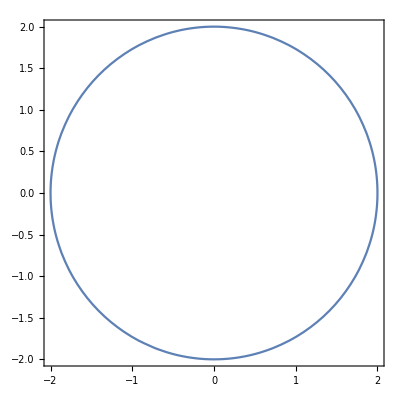

```mathematica
ContourPlot[x^2+y^2==4,{x,-2,2},{y,-2,2}]
```

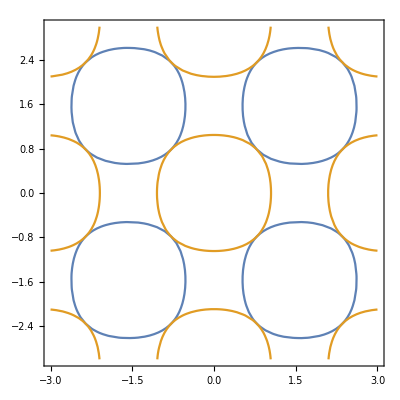

```mathematica
ContourPlot[{Abs[Sin[x]Sin[y]]==0.5,Abs[Cos[x]Cos[y]]==0.5},{x,-3,3},{y,-3,3}]
```

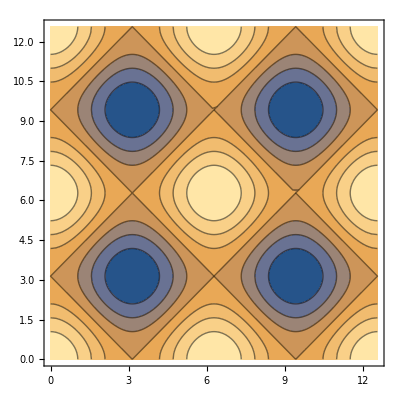

```mathematica
ContourPlot[Sin[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
```

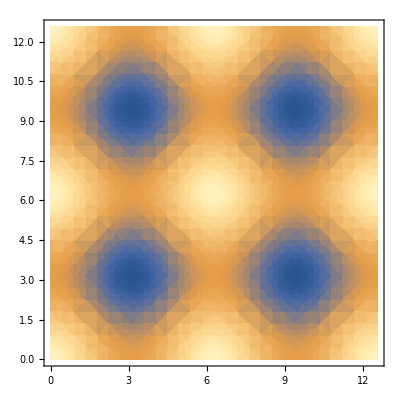

```mathematica
DensityPlot[Cos[x]+Cos[y],{x,0,4Pi},{y,0,4Pi}]
```

## Comandos Gráficos

### Gráficos en Tres Dimensiones

```mathematica
Plot3D[Cos[x]+Cos[y],{x,0,6π},{y,0,6π}]
```

-Graphics3D-

```mathematica
Plot3D[{Sin[x y],Cos[x],Cos[x^2+y]},{x,0,π},{y,0,π}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],0.3t},{t,0,15}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t] (3+Cos[u]),Sin[t] (3+Cos[u]),Sin[u]},{t,0,2 π},{u,0,2 π}]
```

-Graphics3D-

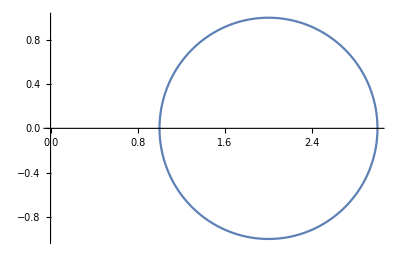

```mathematica
ParametricPlot[{2+Cos[t],Sin[t]},{t,0,2π},PlotRange->{{0,3},{-1,1}}]
```

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2π}]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+2Cos[2θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-

## Comandos Gráficos

### Gráficos de Lista de Datos

```mathematica
data={1,2,4,8,16,32,64};
```

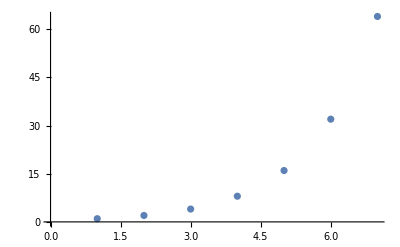

```mathematica
ListPlot[data]
```

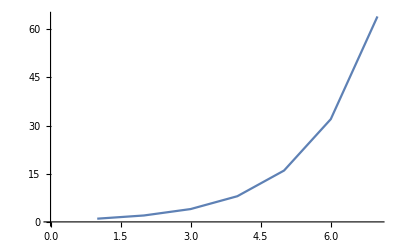

```mathematica
ListLinePlot[data]
```

```mathematica
data={{-1,1},{2,2},{3,4},{5,8},{8,16},{13,32},{21,64}};
```

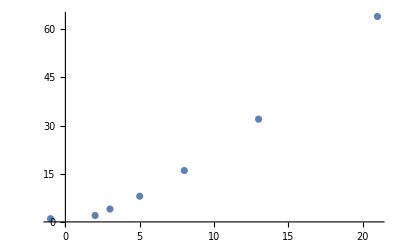

```mathematica
ListPlot[data]
```

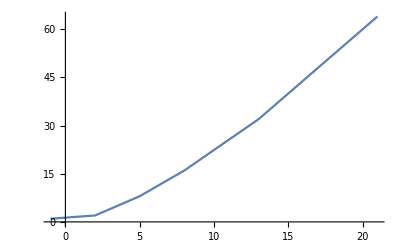

```mathematica
ListLinePlot[data]
```

```mathematica
data1={1,2,3,5,8,13,21};
data2={1,2,4,8,16,32,64};
```

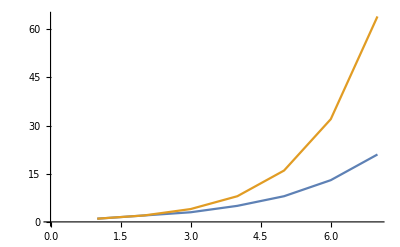

```mathematica
ListLinePlot[{data1,data2}]
```

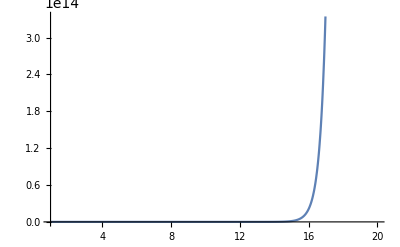

```mathematica
Plot[n!,{n,1,20}]
```

```mathematica
data=Table[{n,n!},{n,1,20,1}]
```

{{1,1},{2,2},{3,6},{4,24},{5,120},{6,720},{7,5040},{8,40320},{9,362880},{10,3628800},{11,39916800},{12,479001600},{13,6227020800},{14,87178291200},{15,1307674368000},{16,20922789888000},{17,355687428096000},{18,6402373705728000},{19,121645100408832000},{20,2432902008176640000}}

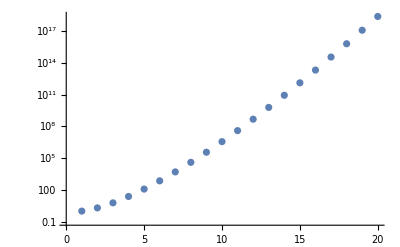

```mathematica
ListLogPlot[data]
```

```mathematica
data=Table[Sin[j^2+i],{i,0,3,0.05},{j,0,3,0.05}];
```

```mathematica
data//Dimensions
```

{61,61}

```mathematica
ListPointPlot3D[data]
```

-Graphics3D-

```mathematica
ListPlot3D[data]
```

-Graphics3D-

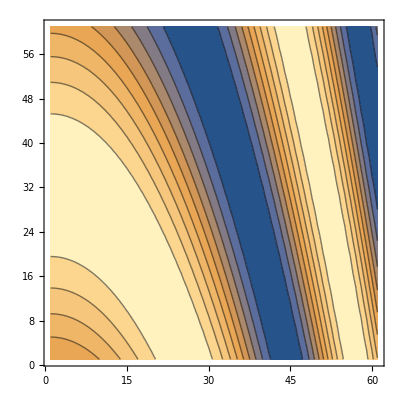

```mathematica
ListContourPlot[data]
```

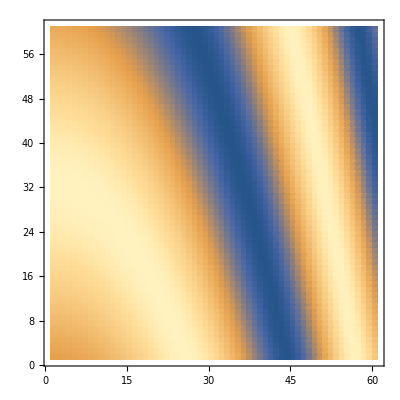

```mathematica
ListDensityPlot[data]
```

```mathematica
data=Flatten[Table[{i,j,Sin[j^2+i]},{i,0,3,0.05},{j,0,3,0.05}],1];
```

```mathematica
data//Dimensions
```

{3721,3}

```mathematica
ListPointPlot3D[data]
```

-Graphics3D-

```mathematica
ListPlot3D[data]
```

-Graphics3D-

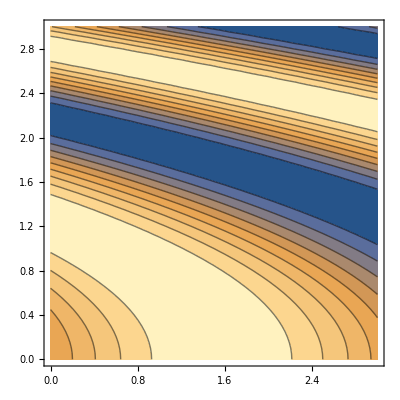

```mathematica
ListContourPlot[data]
```

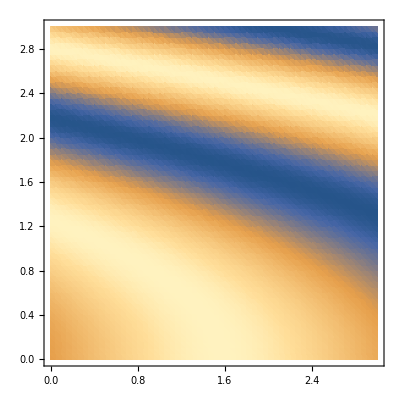

```mathematica
ListDensityPlot[data]
```

## Comandos Gráficos

### Gráficos de Tipo Especial 2D

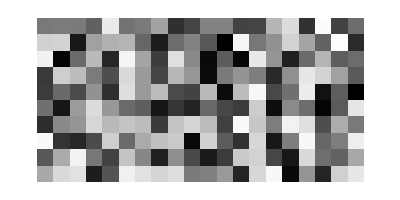

```mathematica
data=RandomReal[1,{10,20}];
ArrayPlot[data]
```

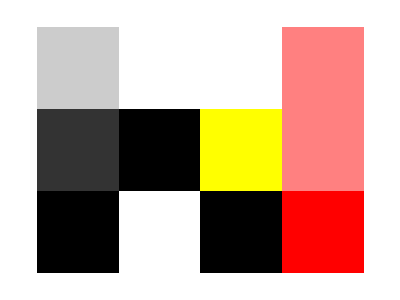

```mathematica
data={{0.2,0,0,Pink},{0.8,1,Yellow,Pink},{1,0,1,Red}};
ArrayPlot[data]
```

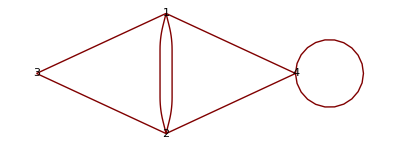

```mathematica
relations={1->2,2->1,3->1,3->2,4->1,4->2,4->4};
GraphPlot[relations,VertexLabeling->True]
```

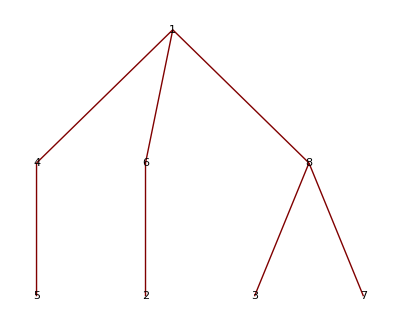

```mathematica
relations={1->4,1->6,1->8,2->6,3->8,4->5,7->8};
TreePlot[relations,VertexLabeling->True]
```

```mathematica
data=RandomInteger[{1,200},{10}]
```

{129,188,167,194,189,54,71,127,132,37}

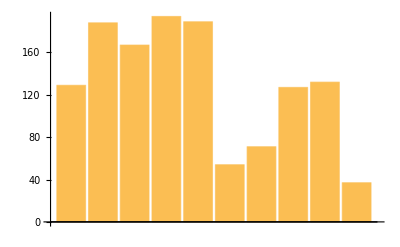

```mathematica
BarChart[data]
```

```mathematica
PieChart[data]
```

-Graphics-

```mathematica
data=RandomReal[1,{10,3}];
BubbleChart[data]
```

-Graphics-

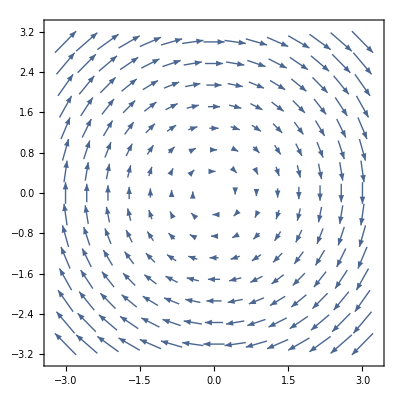

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3}]
```

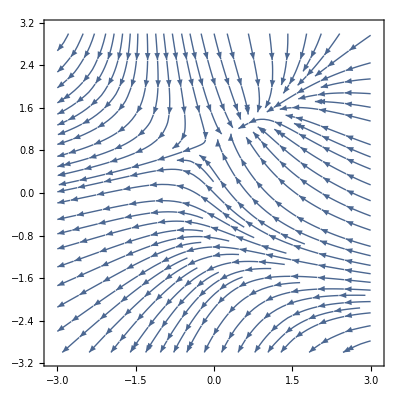

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

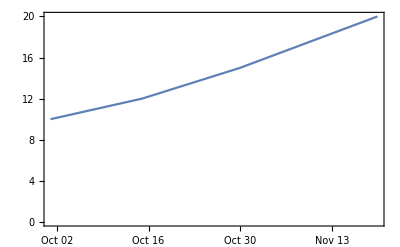

```mathematica
data={{{2006,10,1},10},{{2006,10,15},12},{{2006,10,30},15},{{2006,11,20},20}};

DateListPlot[data]
```

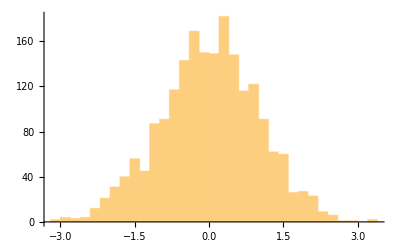

```mathematica
data=RandomVariate[NormalDistribution[0,1],2000];
Histogram[data]
```

### Gráficos de Tipo Especial 3D

```mathematica
relations={1->2,1->3,1->4,1->5,2->3,2->4,2->5,3->4,3->5,4->5};GraphPlot3D[relations,VertexLabeling->True,Boxed->False]
```

-Graphics3D-

```mathematica
BarChart3D[{10,2,3,5,10}]
```

-Graphics3D-

```mathematica
PieChart3D[{1,2,3,4}]
```

-Graphics3D-

```mathematica
data=RandomReal[1,{10,4}];
BubbleChart3D[data]
```

-Graphics3D-

```mathematica
VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

```mathematica
data=RandomVariate[NormalDistribution[0,1],{1000,2}];
Histogram3D[data]
```

-Graphics3D-

## Usando Opciones

### Opciones Asociadas a un Símbolo

Options[f]						Gives a list of default options for f
Options[f] = {opts}					Define options for f
SetOptions[f, opt_1→val_1,…]			Set the default options for f

#### FindRoot

```mathematica
Options[FindRoot]
```

{AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
FindRoot[Cos[x]-x==0,{x,1}]
```

{x→0.739085}

```mathematica
FindRoot[Cos[x]-x==0,{x,1},WorkingPrecision->30]
```

{x→0.739085133215160641655312087674}

```mathematica
Reap[FindRoot[Cos[x]-x==0,{x,1},EvaluationMonitor:>Sow[x]]]
```

{{x→0.739085},{{1.,0.750364,0.739113,0.739085,0.739085}}}

```mathematica
Reap[FindRoot[Cos[x]-x==0,{x,1},WorkingPrecision->30,EvaluationMonitor:>Sow[x]]]
```

{{x→0.739085133215160641655312087674},{{1.,0.750363867840243893034942306682,0.739112890911361670360585290905,0.739085133385283969760125120857,0.739085133215160641661702625685,0.739085133215160641655312087674}}}

```mathematica
Reap[FindRoot[Cos[x]-x==0,{x,1},EvaluationMonitor:>Sow[x],WorkingPrecision->30]]
```

{{x→0.739085133215160641655312087674},{{1.,0.750363867840243893034942306682,0.739112890911361670360585290905,0.739085133385283969760125120857,0.739085133215160641661702625685,0.739085133215160641655312087674}}}

#### Integrate

```mathematica
Options[Integrate]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
Integrate[x^n,{x,0,1}]
```

ConditionalExpression[1/(1+n),Re[n]>-1]

```mathematica
Integrate[x^n,{x,0,1},GenerateConditions->False]
```

1/(1+n)

```mathematica
Integrate[x^n,{x,a,b}]
```

ConditionalExpression[-(a^(1+n)-b^(1+n))/(1+n),Re[a]≥0&&Re[b]≥0&&((Re[a/(-a+b)]≥0&&a/(a-b)≠0)||a/(a-b)∉ℝ||Re[a/(a-b)]>1)]

```mathematica
Integrate[x^n,{x,a,b},GenerateConditions->False]
```

(-a^(1+n)+b^(1+n))/(1+n)

```mathematica
Integrate[x^n,{x,0,1},Assumptions->n>0]
```

1/(1+n)

```mathematica
Integrate[x^(1/n),{x,0,1},Assumptions->n>0]
```

n/(1+n)

```mathematica
SetOptions[Integrate,Assumptions->n>0]
```

{Assumptions→n>0,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
Integrate[x^n,{x,0,1}]
```

1/(1+n)

```mathematica
Integrate[x^(1/n),{x,0,1}]
```

n/(1+n)

```mathematica
Refine[√(n^2)]
```

√(n^2)

```mathematica
SetOptions[Integrate,Assumptions:>$Assumptions]
```

{Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
$Assumptions
```

True

```mathematica
$Assumptions=n>0
```

n>0

```mathematica
Integrate[x^n,{x,0,1}]
```

1/(1+n)

```mathematica
Options[Refine]
```

{Assumptions:>$Assumptions,TimeConstraint→30}

```mathematica
Refine[√(n^2)]
```

n

```mathematica
$Assumptions=True
```

True

#### New function f with options

```mathematica
Options[f]={a->1,b->2,"c"->3}
```

{a→1,b→2,c→3}

```mathematica
f[x__,OptionsPattern[]]:= {x,OptionValue[a],OptionValue[b],OptionValue["c"]}
```

```mathematica
{f[x],f[x,y,z],f[x,a->17],f[x,"c"->18]}
```

{{x,1,2,3},{x,y,z,1,2,3},{x,17,2,3},{x,1,2,18}}

```mathematica
{f[x,y,z,a->17,b->18],f[x,y,z,b->18,a->17]}
```

{{x,y,z,17,18,3},{x,y,z,17,18,3}}

```mathematica
SetOptions[f,a->0]
```

{a→0,b→2,c→3}

```mathematica
{f[x],f[x,y],f[x,a->17],f[x,b->18],f[x,a->17,b->18],f[x,b->18,a->17]}
```

{{x,0,2,3},{x,y,0,2,3},{x,17,2,3},{x,0,18,3},{x,17,18,3},{x,17,18,3}}

### Opciones en los Gráficos

#### Plot

```mathematica
Options[Plot]//Length
```

62

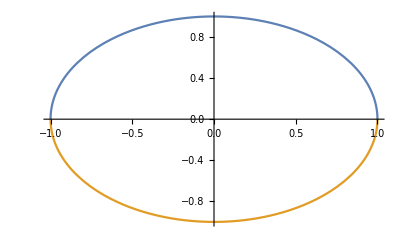

```mathematica
Plot[{√(1-x^2),-√(1-x^2)},{x,-1,1}]
```

```mathematica
Plot[{√(1-x^2),-√(1-x^2)},{x,-1,1},AspectRatio->1/GoldenRatio]
```

-Graphics-

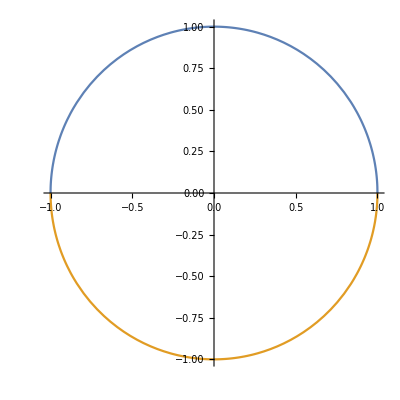

```mathematica
Plot[{√(1-x^2),-√(1-x^2)},{x,-1,1},AspectRatio->1]
```

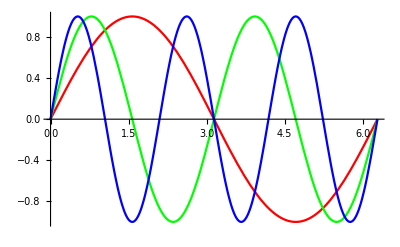

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Red,Green,Blue}]
```

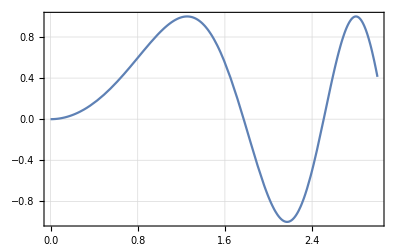

```mathematica
Plot[Sin[x^2],{x,0,3},Frame->True,GridLines->Automatic]
```

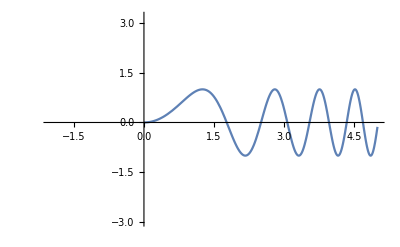

```mathematica
Plot[Sin[x^2],{x,0,5},PlotRange->{{-2,5},{-3,3.2}}]
```

```mathematica
SetOptions[Plot,PlotStyle->Dashing[{.05,.01}]];
```

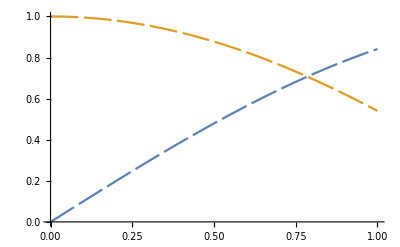

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,1}]
```

```mathematica
SetOptions[Plot,PlotStyle->Automatic];
```

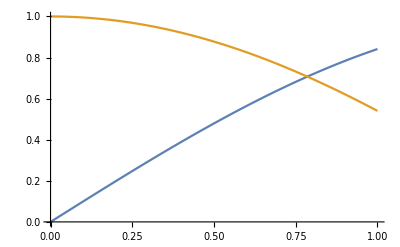

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,1}]
```

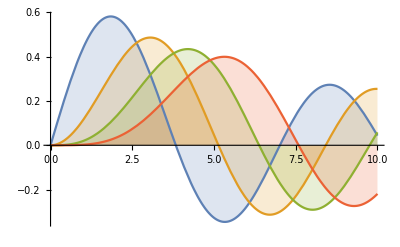

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

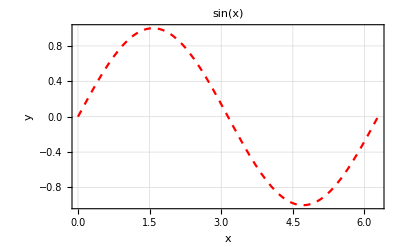

```mathematica
Plot[Sin[x],{x,0,2 π},Frame->True,GridLines->Automatic,PlotLabel->"sin(x)",PlotStyle->{Dashed,Red},FrameLabel->{
"x","y"}]
```

```mathematica
Plot[Sin[x], {x,0,2π}, PlotTheme->"Marketing"]
```

-Graphics-

#### ListPlot

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelingFunction→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

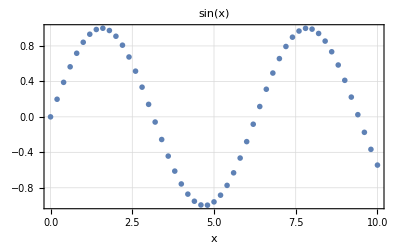

```mathematica
ListPlot[Table[{x,Sin[x]},{x,0,10,0.2}],
Frame->True,GridLines->Automatic,PlotLabel->"sin(x)",PlotMarkers->{"🐺",Small},FrameTicks->True,Axes->False,FrameLabel->{{None,y},{x,"plot"}}]
```

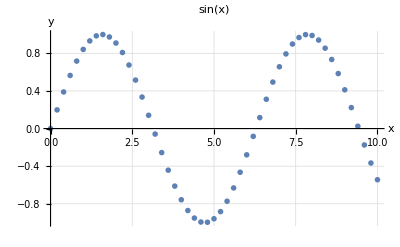

```mathematica
ListPlot[Table[{x,Sin[x]},{x,0,10,0.2}],
GridLines->Automatic,AxesLabel->{x,y},
PlotLabel->"sin(x)",PlotMarkers->{"🐺",Small},Ticks->True]
```

#### PolarPlot

```mathematica
Options[PolarPlot]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→Automatic,AxesLabel→None,AxesOrigin→{0,0},AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#3&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PolarAxes→False,PolarAxesOrigin→Automatic,PolarGridLines→None,PolarTicks→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
PolarPlot[1,{x,0,2π}]
```

-Graphics-

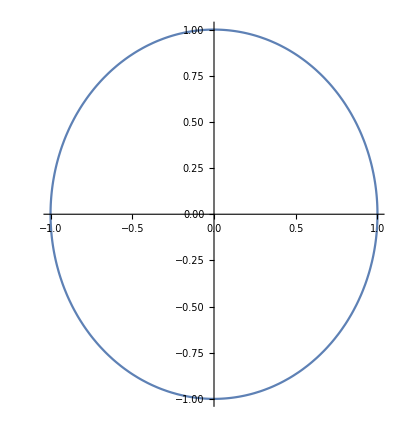

```mathematica
(*mi pantalla*)
PolarPlot[1,{x,0,2π},AspectRatio->(1920/1080)/(1280/800)]
```

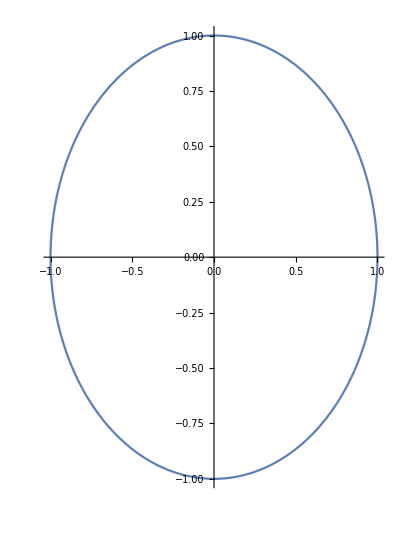

```mathematica
(*para el lcd*)
PolarPlot[1,{x,0,2π},AspectRatio->(1920/1080)/(1024/768)]
```

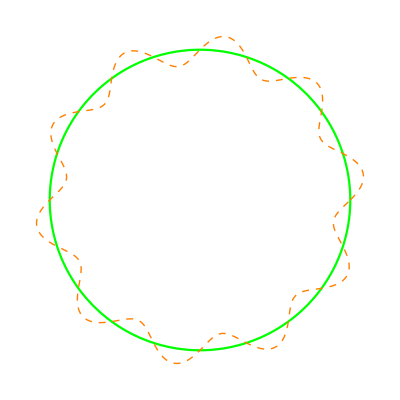

```mathematica
PolarPlot[{1,1+1/10 Sin[10t]},{t,0,2Pi},PlotStyle->{Green,Directive[Dashed,Thick,Orange]},
Axes->False,AspectRatio->1]
```

#### ContourPlot

```mathematica
Options[ContourPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→None,BoxRatios→Automatic,ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ContourLabels→Automatic,ContourLines→True,Contours→Automatic,ContourShading→Automatic,ContourStyle→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},LightingAngle→None,MaxRecursion→Automatic,Mesh→None,MeshFunctions→{},MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

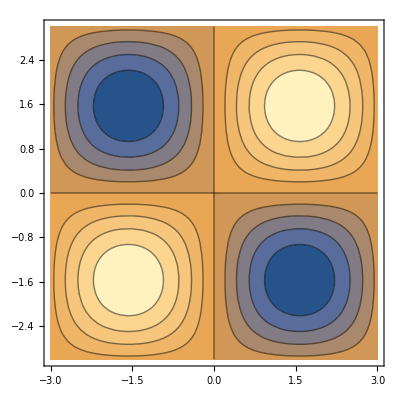

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3}]
```

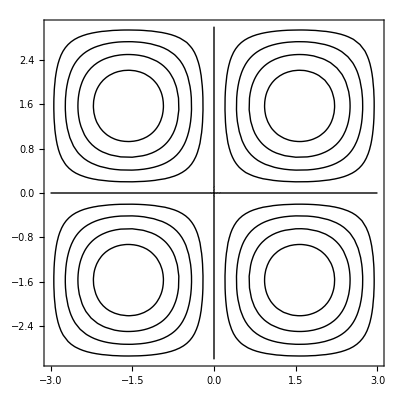

```mathematica
ContourPlot[Sin[x]Sin[y],{x,-3,3},{y,-3,3},ContourShading->None]
```

#### BarChart

```mathematica
Options[BarChart]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BarSpacing→Automatic,BaselinePosition→Automatic,BaseStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,Joined→False,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

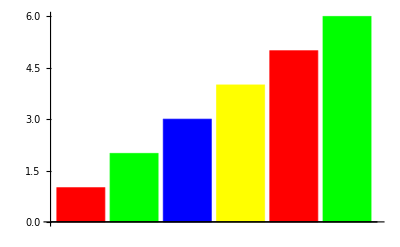

```mathematica
BarChart[{1,2,3,4,5,6},ChartStyle->{Red,Green,Blue,Yellow}]
```

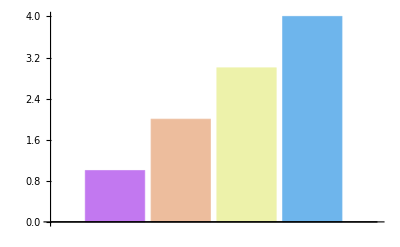

```mathematica
BarChart[{1,2,3,4},ChartStyle->"Pastel"]
```

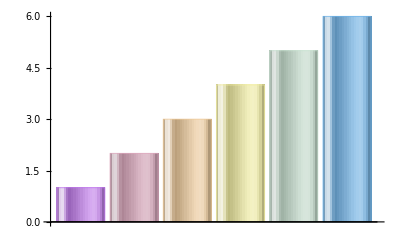

```mathematica
BarChart[Range[6],ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel"]
```

#### Plot3D

```mathematica
Options[Plot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,ScalingFunctions→None,SphericalRegion→False,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},Axes->{False,False,True},
FaceGrids->All]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotStyle->None,Boxed->False,Axes->False]
```

-Graphics3D-

## Regraficando y Combinando Gráficos

Show[plot,option → value]					redraw a plot with options changed
Show[plot1,plot2,…]						combine several plots

GraphicsGrid[{{plo11,plo12,…},…}] 				draw a rectangular array of plots
GraphicsRow[{plo1,plot2,…}]					draw several plots side by side
GraphicsColumn[{plot1,plot2,…}]				draw a column of plots

#### Regraficando

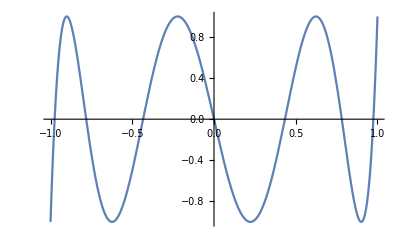

```mathematica
g=Plot[ChebyshevT[7,x],{x,-1,1}]
```

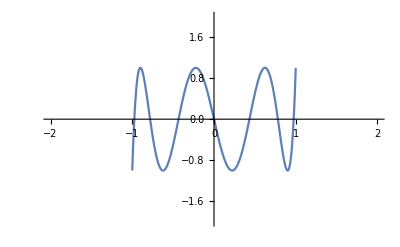

```mathematica
Show[g,PlotRange->{{-2,2},{-2,2}}]
```

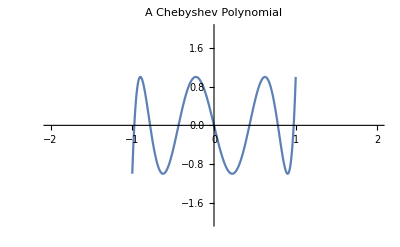

```mathematica
Show[%,PlotLabel->"A Chebyshev Polynomial"]
```

#### Combinando Gráficos

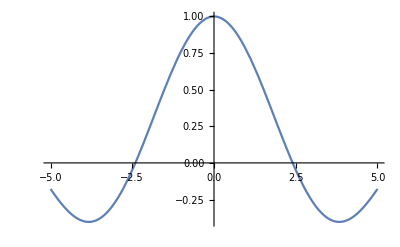

```mathematica
gj0=Plot[BesselJ[0,x],{x,-5,5}]
```

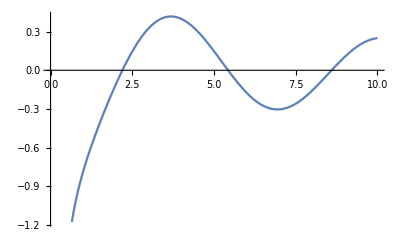

```mathematica
gy1=Plot[BesselY[1,x],{x,0,10}]
```

```mathematica
Options[gj0,PlotRange]
```

{PlotRange→{{-5,5},{-0.402759,1.}}}

```mathematica
Options[gy1,PlotRange]
```

{PlotRange→{{0,10},{-1.17423,0.41673}}}

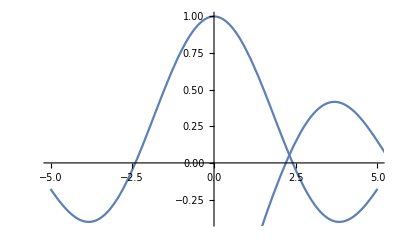

```mathematica
Show[gj0,gy1]
```

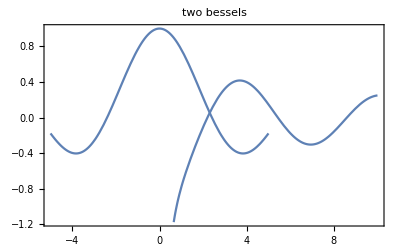

```mathematica
Show[gj0,gy1,PlotRange->Automatic,Frame->True,PlotLabel->"two bessels"]
```

```mathematica
g1=Plot3D[Sin[x y],{x,0,3},{y,0,3}]
```

-Graphics3D-

```mathematica
g2=Plot3D[Cos[x-y],{x,0,3},{y,0,3}]
```

-Graphics3D-

```mathematica
Show[g1,g2]
```

-Graphics3D-

#### Graphics grids


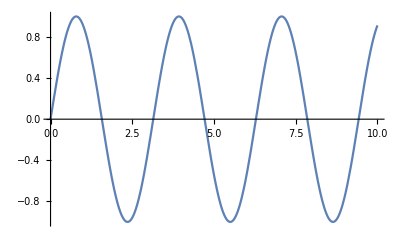
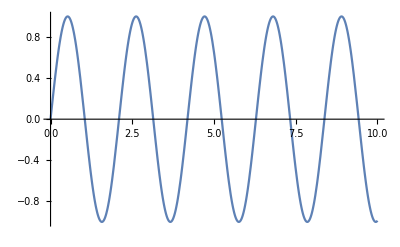
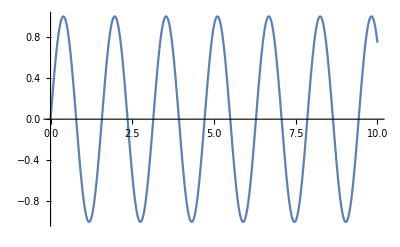

```mathematica
tplots=Table[Plot[Sin[ω x],{x,0,10}],{ω,1,4,1}]
```

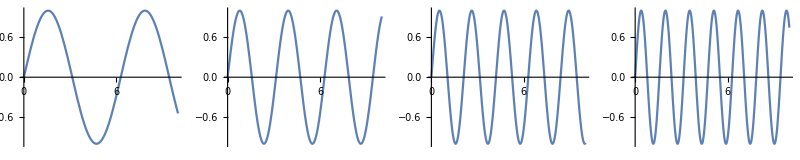

```mathematica
GraphicsRow[tplots,ImageSize->800,Frame->{}]
```

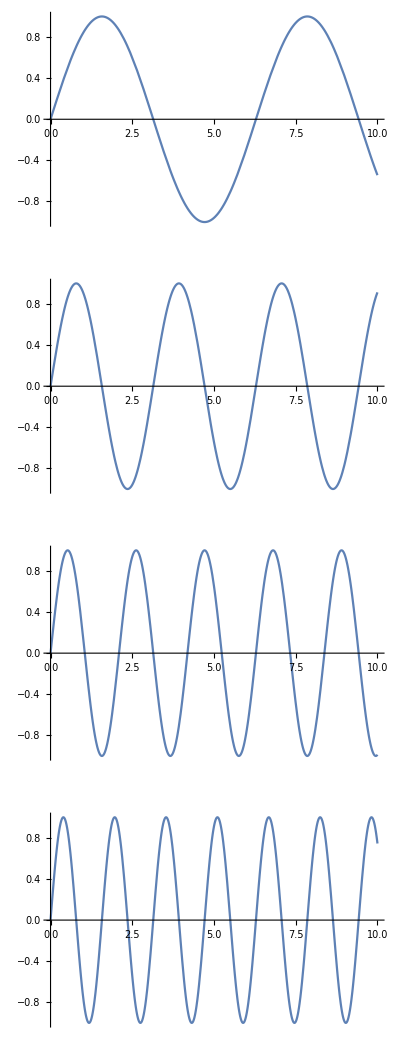

```mathematica
GraphicsColumn[tplots]
```

```mathematica
Options[GraphicsGrid]
```

{Alignment→{Center,Center},AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DefaultBaseStyle→GraphicsGrid,DisplayFunction:>$DisplayFunction,Dividers→None,Epilog→{},FormatType:>TraditionalForm,Frame→None,FrameLabel→None,FrameStyle→Automatic,FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,ItemAspectRatio→Automatic,LabelStyle→{},Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Spacings→Scaled[0.1],Ticks→Automatic,TicksStyle→{}}

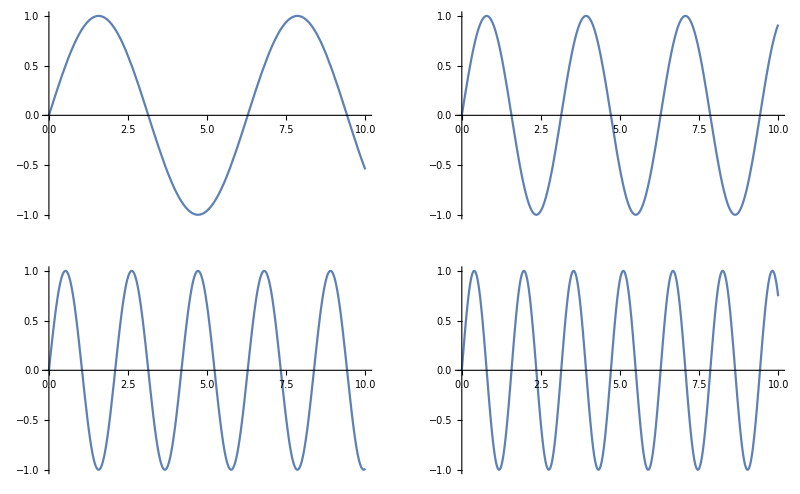

```mathematica
GraphicsGrid[Partition[tplots,2],Frame->True]
```

#### Ejemplo: Ajuste a una recta

```mathematica
xdata = {0.00, 0.10, 0.20, 0.30, 0.40, 0.50, 0.60, 0.70, 0.80, 0.90, 1.00};
ydata = {-0.102900, .373642, 2.437483, 3.938363, 3.312305, 5.494725, 5.433256, 6.393219, 9.060489, 9.364169, 9.52066};
data = Transpose[{xdata, ydata}];
```

```mathematica
f=Fit[data,{1,x},x]
```

-0.0240349+10.0891 x

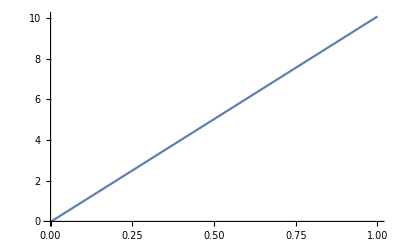

```mathematica
p1=Plot[f,{x,0,1}]
```

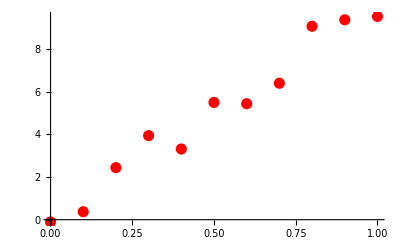

```mathematica
p2=ListPlot[data,PlotStyle->{Hue[0],PointSize[0.02]}]
```

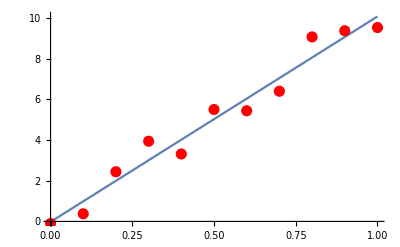

```mathematica
Show[p1,p2]
```

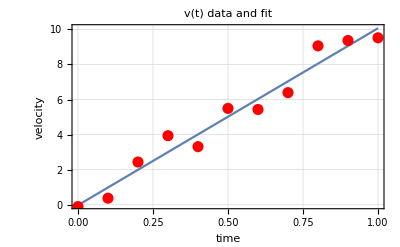

```mathematica
p=Show[p1,p2,PlotLabel->"v(t) data and fit",FrameLabel->{"time","velocity"},Frame->True,TextStyle->{FontFamily->"Frutiger"},GridLines->Automatic]
```

```mathematica
Export["./im.gif",p,"GIF"]
```

./im.gif

```mathematica
SystemOpen["im.gif"]
```

```mathematica
fontlist=FE`Evaluate[FEPrivate`GetPopupList["MenuListFonts"]]
```

{Abyssinica SIL→Abyssinica SIL,Alegreya SC→Alegreya SC,Bitstream Charter→Bitstream Charter,Bitstream Vera Sans→Bitstream Vera Sans,Bitstream Vera Sans Mono→Bitstream Vera Sans Mono,Bitstream Vera Serif→Bitstream Vera Serif,Century Schoolbook L→Century Schoolbook L,Clear Sans→Clear Sans,Clear Sans Light→Clear Sans Light,Clear Sans Medium→Clear Sans Medium,Clear Sans Thin→Clear Sans Thin,Courier→Courier,Courier 10 Pitch→Courier 10 Pitch,Cousine→Cousine,DejaVu Sans→DejaVu Sans,DejaVu Sans Mono→DejaVu Sans Mono,DejaVu Serif→DejaVu Serif,Dingbats→Dingbats,Droid Serif→Droid Serif,EB Garamond→EB Garamond,EB Garamond 12 All SC→EB Garamond 12 All SC,EB Garamond SC→EB Garamond SC,Economica→Economica,Felipa→Felipa,FreeMono→FreeMono,FreeSans→FreeSans,FreeSerif→FreeSerif,Garuda→Garuda,Gentium Basic→Gentium Basic,Inconsolata→Inconsolata,KacstArt→KacstArt,KacstBook→KacstBook,KacstDecorative→KacstDecorative,KacstDigital→KacstDigital,KacstFarsi→KacstFarsi,KacstLetter→KacstLetter,KacstNaskh→KacstNaskh,KacstOffice→KacstOffice,KacstOne→KacstOne,KacstPen→KacstPen,KacstPoster→KacstPoster,KacstQurn→KacstQurn,KacstScreen→KacstScreen,KacstTitle→KacstTitle,KacstTitleL→KacstTitleL,Kalam→Kalam,Khmer OS→Khmer OS,Khmer OS System→Khmer OS System,Kinnari→Kinnari,Laksaman→Laksaman,Latin Modern Math→Latin Modern Math,Latin Modern Mono→Latin Modern Mono,Latin Modern Mono Caps→Latin Modern Mono Caps,Latin Modern Mono Light→Latin Modern Mono Light,Latin Modern Mono Light Cond→Latin Modern Mono Light Cond,Latin Modern Mono Prop→Latin Modern Mono Prop,Latin Modern Mono Prop Light→Latin Modern Mono Prop Light,Latin Modern Mono Slanted→Latin Modern Mono Slanted,Latin Modern Roman→Latin Modern Roman,Latin Modern Roman Caps→Latin Modern Roman Caps,Latin Modern Roman Demi→Latin Modern Roman Demi,Latin Modern Roman Dunhill→Latin Modern Roman Dunhill,Latin Modern Roman Slanted→Latin Modern Roman Slanted,Latin Modern Roman Unslanted→Latin Modern Roman Unslanted,Latin Modern Sans→Latin Modern Sans,Latin Modern Sans Demi Cond→Latin Modern Sans Demi Cond,Latin Modern Sans Quotation→Latin Modern Sans Quotation,Lato→Lato,League Gothic→League Gothic,Liberation Mono→Liberation Mono,Liberation Sans→Liberation Sans,Liberation Sans Narrow→Liberation Sans Narrow,Liberation Serif→Liberation Serif,LKLUG→LKLUG,Lohit Punjabi→Lohit Punjabi,Loma→Loma,Mathematica→Mathematica,MathematicaMono→MathematicaMono,MathematicaSans→MathematicaSans,Monospace→Monospace,mry_KacstQurn→mry_KacstQurn,NanumBarunGothic→NanumBarunGothic,NanumGothic→NanumGothic,NanumMyeongjo→NanumMyeongjo,Nimbus Mono L→Nimbus Mono L,Nimbus Roman No9 L→Nimbus Roman No9 L,Nimbus Sans L→Nimbus Sans L,Norasi→Norasi,Noto Sans CJK JP→Noto Sans CJK JP,Noto Sans CJK KR→Noto Sans CJK KR,Noto Sans CJK SC→Noto Sans CJK SC,Noto Sans CJK TC→Noto Sans CJK TC,Noto Sans Mono CJK JP→Noto Sans Mono CJK JP,Noto Sans Mono CJK KR→Noto Sans Mono CJK KR,Noto Sans Mono CJK SC→Noto Sans Mono CJK SC,Noto Sans Mono CJK TC→Noto Sans Mono CJK TC,OpenSymbol→OpenSymbol,Oswald→Oswald,Padauk→Padauk,Padauk Book [PYRS]→Padauk Book [PYRS],Padauk Book [SIL ]→Padauk Book [SIL ],Phetsarath OT→Phetsarath OT,Playfair Display→Playfair Display,Purisa→Purisa,Roboto→Roboto,Roboto Condensed→Roboto Condensed,Roboto Slab→Roboto Slab,Saab→Saab,Sans Serif→Sans Serif,Sawasdee→Sawasdee,Serif→Serif,Shadows Into Light Two→Shadows Into Light Two,Source Code Pro→Source Code Pro,Source Sans Pro→Source Sans Pro,Source Serif Pro→Source Serif Pro,Standard Symbols L→Standard Symbols L,STIX→STIX,STIX Math→STIX Math,STIXGeneral→STIXGeneral,STIXIntegralsD→STIXIntegralsD,STIXIntegralsSm→STIXIntegralsSm,STIXIntegralsUp→STIXIntegralsUp,STIXIntegralsUpD→STIXIntegralsUpD,STIXIntegralsUpSm→STIXIntegralsUpSm,STIXNonUnicode→STIXNonUnicode,STIXSizeFiveSym→STIXSizeFiveSym,STIXSizeFourSym→STIXSizeFourSym,STIXSizeOneSym→STIXSizeOneSym,STIXSizeThreeSym→STIXSizeThreeSym,STIXSizeTwoSym→STIXSizeTwoSym,STIXVariants→STIXVariants,Swiss 721→Swiss 721,Symbola→Symbola,TakaoPGothic→TakaoPGothic,TeX Gyre Adventor→TeX Gyre Adventor,TeX Gyre Bonum→TeX Gyre Bonum,TeX Gyre Bonum Math→TeX Gyre Bonum Math,TeX Gyre Chorus→TeX Gyre Chorus,TeX Gyre Cursor→TeX Gyre Cursor,TeX Gyre Heros→TeX Gyre Heros,TeX Gyre Heros Cn→TeX Gyre Heros Cn,TeX Gyre Pagella→TeX Gyre Pagella,TeX Gyre Pagella Math→TeX Gyre Pagella Math,TeX Gyre Schola→TeX Gyre Schola,TeX Gyre Schola Math→TeX Gyre Schola Math,TeX Gyre Termes→TeX Gyre Termes,TeX Gyre Termes Math→TeX Gyre Termes Math,Tibetan Machine Uni→Tibetan Machine Uni,Titillium Web→Titillium Web,Tlwg Mono→Tlwg Mono,Tlwg Typewriter→Tlwg Typewriter,Tlwg Typist→Tlwg Typist,Tlwg Typo→Tlwg Typo,Ubuntu→Ubuntu,Ubuntu Condensed→Ubuntu Condensed,Ubuntu Mono→Ubuntu Mono,Umpush→Umpush,URW Bookman L→URW Bookman L,URW Chancery L→URW Chancery L,URW Gothic L→URW Gothic L,URW Palladio L→URW Palladio L,Utopia→Utopia,Waree→Waree,Yanone Kaffeesatz→Yanone Kaffeesatz}

## Estructura de los Gráficos

### Estructura de Gráficos en 2D

#### Graphics

Graphics[prim]
Graphics[prim, opts]
Graphics[{dir1, dir2, prim}]
Graphics[{{dir11, dir12, ..., prim1}, {dir21, dir22, ..., prim2}, ...}]

#### Primitives

Point[p] 				    	Point at p
Point[{p1,...,pn}] 				Points at p1,...,pn
Line[{p1,...,pn}] 				Line through p1,...,pn
Arrow[{p1,...,pn}] 				Arrow through p1,...,pn
Circle[p,r] 					Circle with center p and radius r
Text[expr,p] 					Text expr centered at p

Disk[p, r] 					Filled circle with center p and radius r
Rectangle[{xa, xb}, {ya, yb}] 		Filled rectangle
Polygon[{p1, ..., pn}] 			Filled polygon with vertices p1, ..., pn

Raster[array]					Rectangular array of gray levels

#### Directives

PointSize[r],							
AbsolutePointSize[r]
r = Small, Large

Thickness[r],						
AbsoluteThickness[r]
Thick

Dashing[{r1,r2,...}],			
AbsoluteDashing[{r1,r2,...}]
Dashed, Dotted

EdgeForm[g]
FaceForm[g]
CapForm[type]
JoinForm[type]

Opacity[a]					opacity a
GrayLevel[g] 					Gray g
RGBColor[r,g,b]				Color with r,g,b componentes
Hue[h] 						Hue hue
Hue[h,s,b]					Hue hue,saturation,brightness

Directive[g1,g2,...]

#### Point

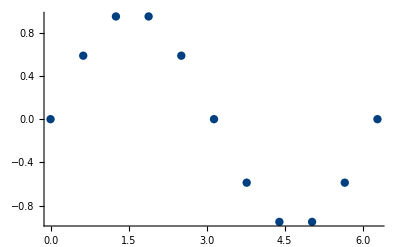

```mathematica
data=Table[{t,Sin[t]},{t,0,2π,2π/10}];
Graphics[{RGBColor[0, 0.25098, 0.501961],AbsolutePointSize[6],Point[data]},Axes->True,AspectRatio->1/GoldenRatio]
```

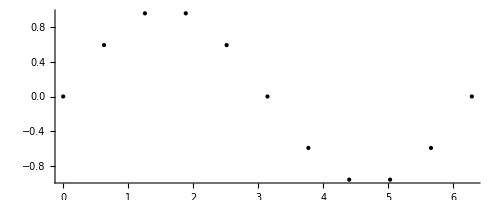

```mathematica
data=Table[{t,Sin[t]},{t,0,2π,2π/10}];
Graphics[Point[data],Axes->True]
```

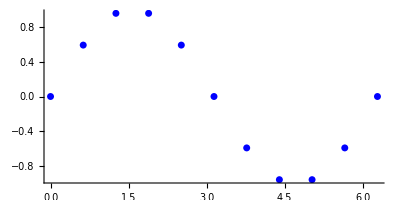

```mathematica
data=Table[{t,Sin[t]},{t,0,2π,2π/10}];
Graphics[{Blue,AbsolutePointSize[5],Point[data]},Axes->True,AspectRatio->1/2]
```

```mathematica
p = Table[{t, Sin[t]}, {t, 0, 2 π, 2 π/10}];
```

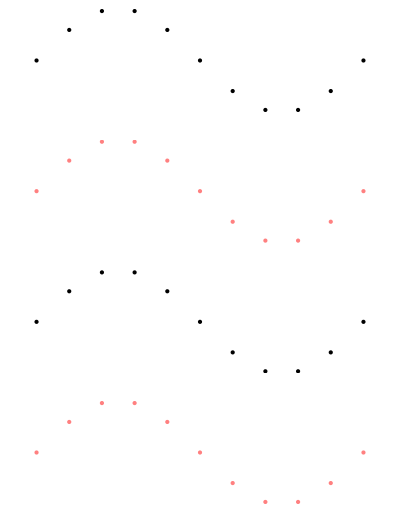

```mathematica
{Graphics[{PointSize[Small],Point[p]}],
Graphics[{PointSize[Small],Pink,Point[p]}],
Graphics[{PointSize[Large],Point[p]}],
Graphics[{PointSize[Large],Pink,Point[p]}]}//GraphicsColumn
```

#### Line

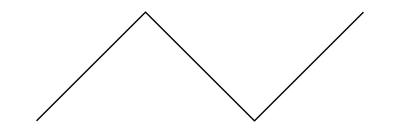

```mathematica
data={{1,0},{2,1},{3,0},{4,1}};
Graphics[Line[data]]
```

```mathematica
l=Line[{{1,0},{2,1},{3,0},{4,1},{5,0},{6,1}}];
```

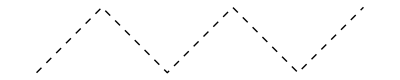
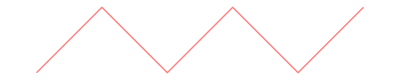
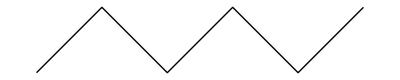
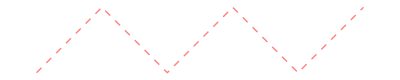

```mathematica
{Graphics[{Dashed,l}],Graphics[{Pink,l}],Graphics[{Thick,l}],Graphics[{Thick,Dashed,Pink,l}]}
```

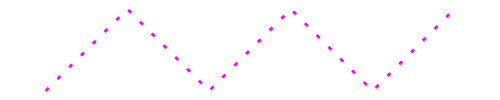

```mathematica
Graphics[{JoinForm["Round"],AbsoluteThickness[2],AbsoluteDashing[{3,9}],RGBColor[1,0,1],l},ImageSize->500]
```

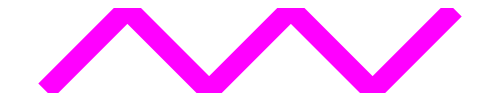

```mathematica
Graphics[{JoinForm["Round"],AbsoluteThickness[15],RGBColor[1,0,1],l},ImageSize->500]
```

#### Arrow

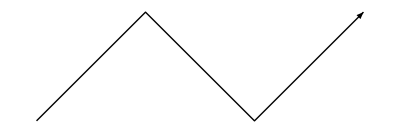

```mathematica
data={{1,0},{2,1},{3,0},{4,1}};
Graphics[Arrow[data]]
```

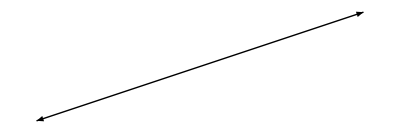

```mathematica
Graphics[{Arrowheads[{-.1,+.1}],Arrow[{{0,0},{1,1/3}}]}]
```

```mathematica
a={Arrowheads[Large],Arrow[{{0,0},{1,.5}}]};
```

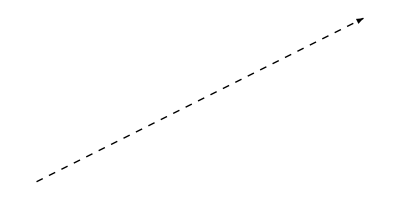
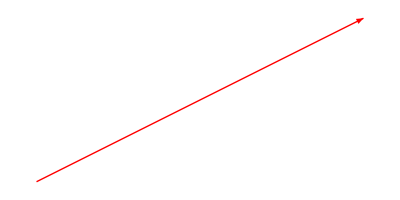
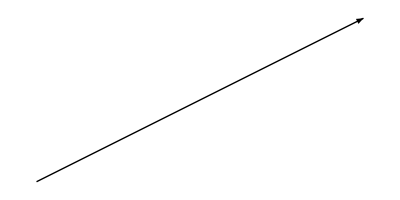
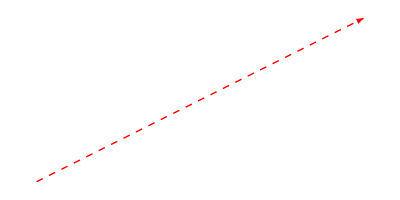

```mathematica
{Graphics[{Dashed,a}],Graphics[{Red,a}],Graphics[{Thick,a}],Graphics[{Thick,Dashed,Red,a}]}
```

#### Circle

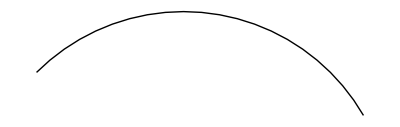

```mathematica
Graphics[Circle[{0,0},1,{Pi/6,3Pi/4}]]
```

```mathematica
{Graphics[{Red,Circle[]}],Graphics[{Thick,Circle[]}],Graphics[{Dashed,Circle[]}],Graphics[{Red,Thick,Dotted,Circle[]}]}/.Graphics[x_]:>Graphics[x,AspectRatio->1/0.75, ImageSize->50]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Disk

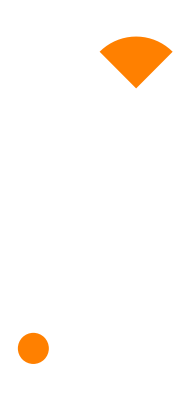

```mathematica
Graphics[{Orange,Disk[{2,5},1,{Pi/4,3Pi/4}],Disk[{0,0},0.3]}]
```

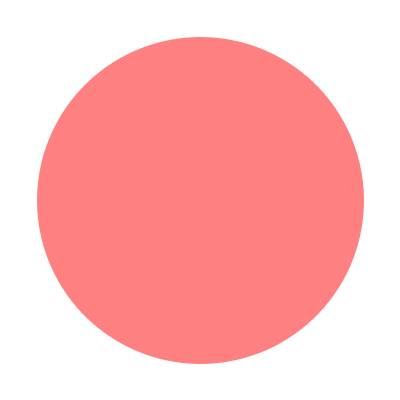
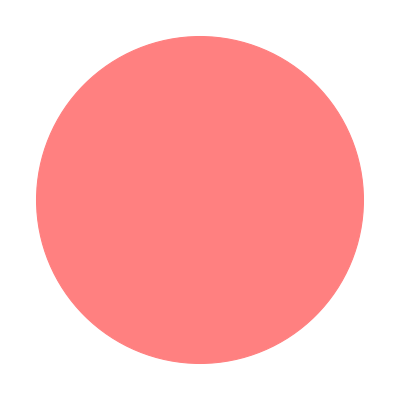
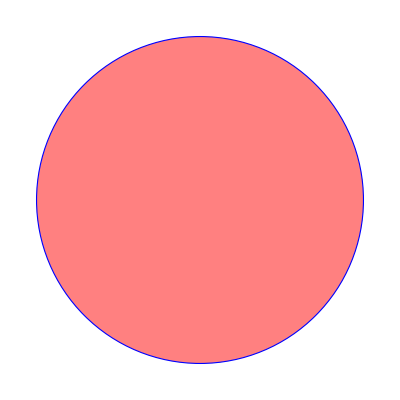
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Graphics[{Pink,Disk[]}],Graphics[{EdgeForm[Thick],Pink,Disk[]}],Graphics[{EdgeForm[Dashed],Pink,Disk[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Disk[]}]}
```

#### Rectangle

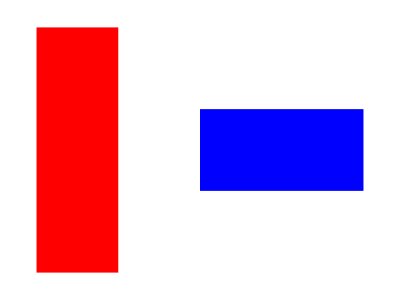

```mathematica
Graphics[{Red,Rectangle[{0,0},{1,3}],Blue,Rectangle[{2,1},{4,2}]}]
```

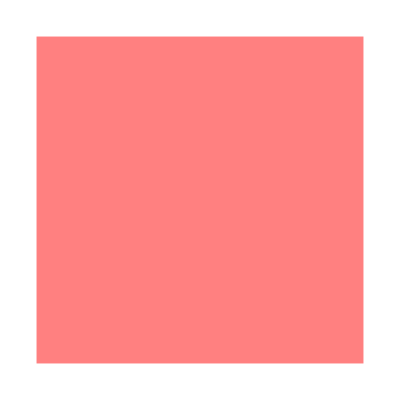
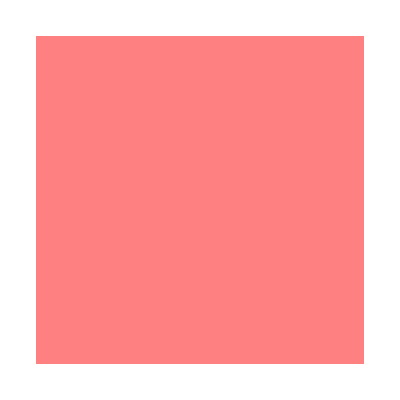
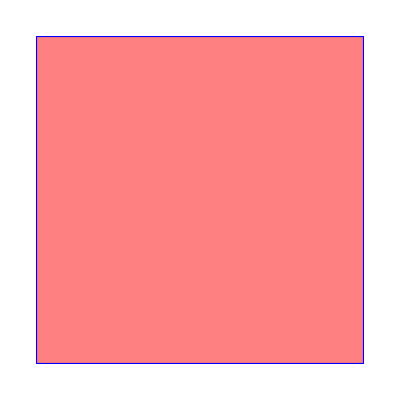
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}
```

#### Polygon

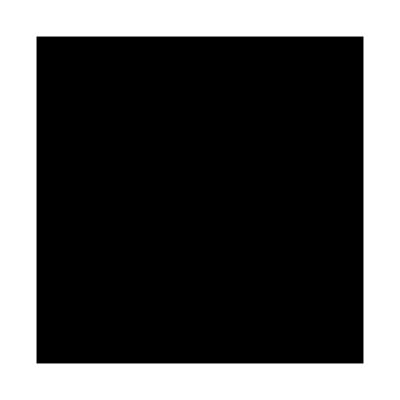

```mathematica
Graphics[Polygon[{{0,0},{0,1},{1,1},{1,0}}]]
```

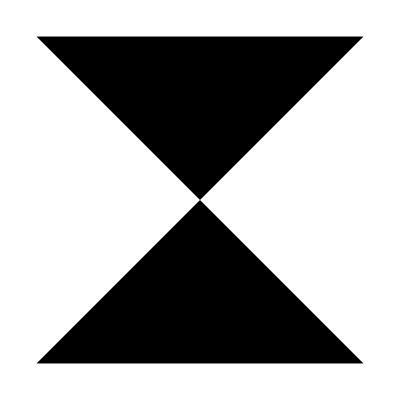

```mathematica
Graphics[Polygon[{{0,0},{1,1},{0,1},{1,0}}]]
```

```mathematica
p=Polygon[{{0,0},{1,1},{0,1},{1,0}}]
```

Polygon[{{0,0},{1,1},{0,1},{1,0}}]

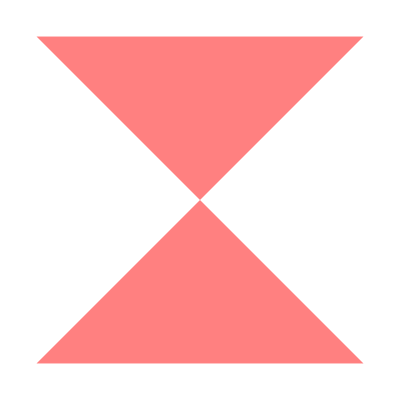
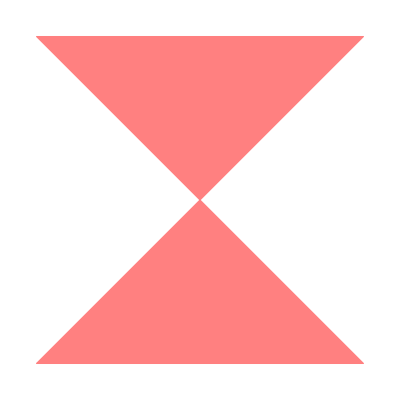
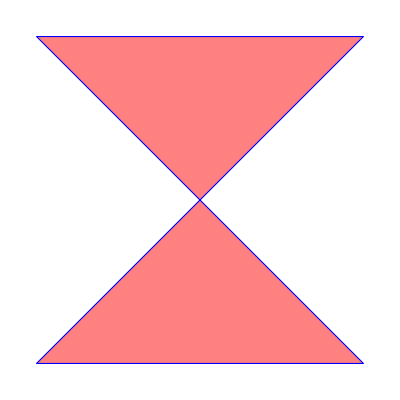
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Graphics[{Pink,p}],Graphics[{EdgeForm[Thick],Pink,p}],Graphics[{EdgeForm[Dashed],Pink,p}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,p}]}
```

#### Text

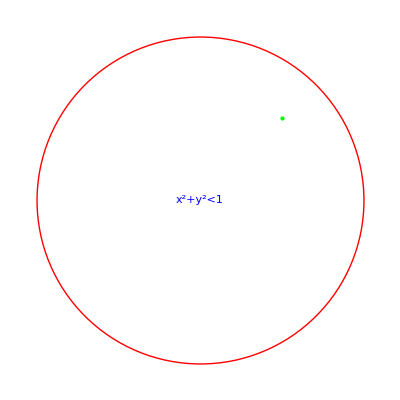

```mathematica
Graphics[{Red,Circle[],{Blue,Style[Text[x^2+y^2<1,{0,0}],34]},Green,Point[{0.5,0.5}]}]
```

#### Raster

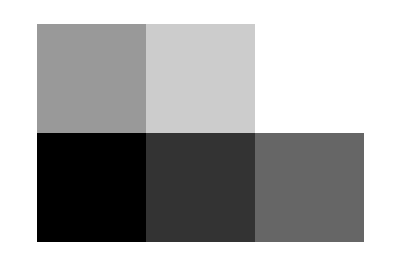

```mathematica
Graphics[Raster[{{0,0.2,0.4},{0.6,0.8,1}}]]
```

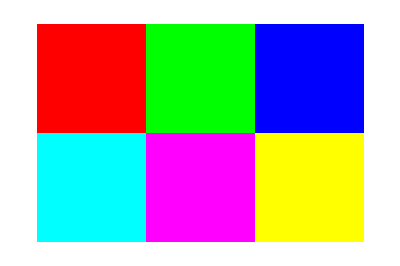

```mathematica
Graphics[Raster[{{{0,1,1},{1,0,1},{1,1,0}},{{1,0,0},{0,1,0},{0,0,1}}}]]
```

#### Ejemplo

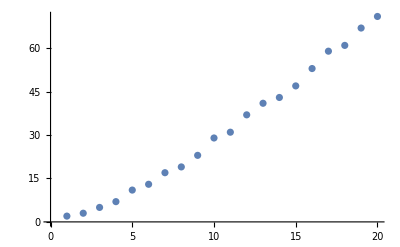

```mathematica
g=ListPlot[Table[Prime[n],{n,20}]]
```

```mathematica
g//InputForm
```

Graphics[{{}, 
  {{{}, {Hue[0.67, 0.6, 0.6], 
     Directive[PointSize[
       0.012833333333333334], 
      RGBColor[0.368417, 0.506779, 
       0.709798], AbsoluteThickness[
       1.6]], Point[{{1., 2.}, {2., 
      3.}, {3., 5.}, {4., 7.}, {5., 
      11.}, {6., 13.}, {7., 17.}, 
      {8., 19.}, {9., 23.}, {10., 
      29.}, {11., 31.}, {12., 37.}, 
      {13., 41.}, {14., 43.}, {15., 
      47.}, {16., 53.}, {17., 59.}, 
      {18., 61.}, {19., 67.}, {20., 
      71.}}]}, {}}}, {}, {}, {}, {}}, 
 {DisplayFunction -> Identity, 
  PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, 
    {Scaled[0.02], Scaled[0.05]}}, 
  AxesOrigin -> {0., 0}, 
  PlotRange -> {{0., 20.}, {0, 71.}}, 
  PlotRangeClipping -> True, 
  ImagePadding -> All, 
  DisplayFunction -> Identity, 
  AspectRatio -> GoldenRatio^(-1), 
  Axes -> {True, True}, 
  AxesLabel -> {None, None}, 
  AxesOrigin -> {0., 0}, 
  DisplayFunction :> Identity, 
  Frame -> {{False, False}, 
    {False, False}}, FrameLabel -> 
   {{None, None}, {None, None}}, 
  FrameTicks -> {{Automatic, 
     Automatic}, {Automatic, 
     Automatic}}, GridLines -> 
   {None, None}, GridLinesStyle -> 
   Directive[GrayLevel[0.5, 0.4]], 
  Method -> 
   {"CoordinatesToolOptions" -> 
     {"DisplayFunction" -> 
       ({(Identity[#1] & )[#1[[1]]], 
         (Identity[#1] & )[
          #1[[2]]]} & ), 
      "CopiedValueFunction" -> 
       ({(Identity[#1] & )[#1[[1]]], 
         (Identity[#1] & )[
          #1[[2]]]} & )}}, 
  PlotRange -> {{0., 20.}, {0, 71.}}, 
  PlotRangeClipping -> True, 
  PlotRangePadding -> 
   {{Scaled[0.02], Scaled[0.02]}, 
    {Scaled[0.02], Scaled[0.05]}}, 
  Ticks -> {Automatic, Automatic}}]

```mathematica
Head[g]
```

Graphics

```mathematica
First[g]
```

{{},{{{},{Hue[0.67, 0.6, 0.6],Directive[PointSize[0.0128333],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Point[{{1.,2.},{2.,3.},{3.,5.},{4.,7.},{5.,11.},{6.,13.},{7.,17.},{8.,19.},{9.,23.},{10.,29.},{11.,31.},{12.,37.},{13.,41.},{14.,43.},{15.,47.},{16.,53.},{17.,59.},{18.,61.},{19.,67.},{20.,71.}}]},{}}},{},{},{},{}}

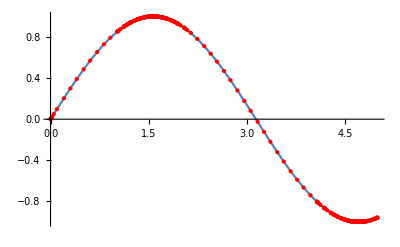

```mathematica
g=Plot[Sin[x],{x,0,5},Mesh->All,MeshStyle->Red]
```

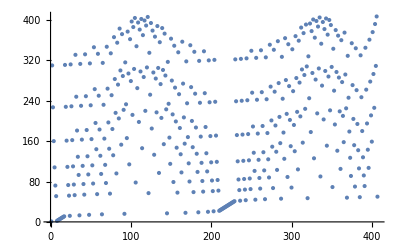

```mathematica
ListPlot[Cases[First[g],Line[x__]:>{x},∞][[1,1]]]
```

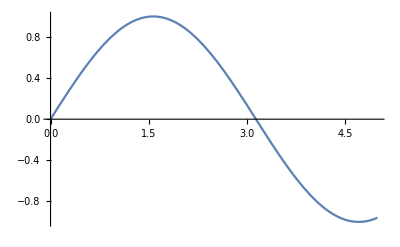

```mathematica
g = Plot[Sin[x], {x,0,5}]
```

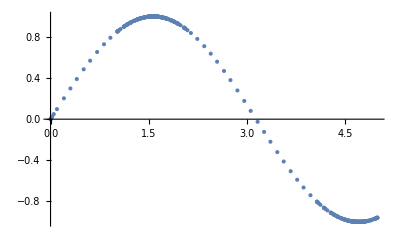

```mathematica
(*Extraer Puntos*)
ListPlot[Cases[First[g], Line[x__]:>{x},∞][[1,1]]]
```

#### Ejemplo

```mathematica
Graphics[{
EdgeForm[Dashed],Green,Disk[{0.6,0.6},0.4],
Blue,{Opacity[0.5], Polygon[{{0,√2},{√2,√2},{√2,0},{0,0}}]},
Red,Thick,Line[{{0,0},{3,0},{2,3},{0,0}}],
Black,Line[{{2,3},{2,0}}],
Style[Text["h",{2.2,1.2}],16],
Line[{{2.08,0},{2.08,0.08},{2,0.08}}],
Green,PointSize[1/10],Point[Scaled[{0.5,0.5}]]
}]
```

-Graphics-

#### Ejemplo

```mathematica
pts=Table[{Cos[2n π/9],Sin[2 n π/9]},{n,0,8}]//N
```

{{1.,0.},{0.766044,0.642788},{0.173648,0.984808},{-0.5,0.866025},{-0.939693,0.34202},{-0.939693,-0.34202},{-0.5,-0.866025},{0.173648,-0.984808},{0.766044,-0.642788}}

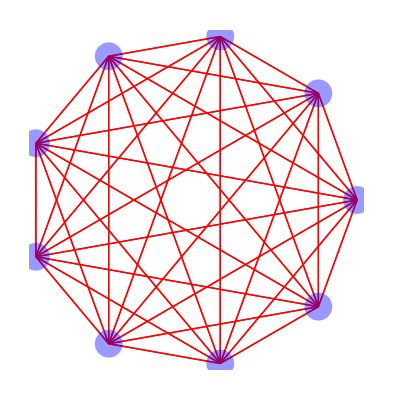

```mathematica
Graphics[{Red,Line[Tuples[pts,2]],Opacity[0.4],Blue,PointSize[0.05],Point[pts]}]
```

```mathematica
Options[plotRegularPolygonWithAllDiagonals]={"LineColor"->Red,"VertexColor"->Blue}
```

{LineColor→RGBColor[1, 0, 0],VertexColor→RGBColor[0, 0, 1]}

```mathematica
plotRegularPolygonWithAllDiagonals[n_,OptionsPattern[]]/;n>=3:=
Module[{pts,k},
pts=Table[{Cos[2k π/n],Sin[2 k π/n]},{k,0,n-1}];
Graphics[{OptionValue["LineColor"],Line[Tuples[pts,2]],Opacity[0.4],OptionValue["VertexColor"],PointSize[0.05],Point[pts]}]]
```

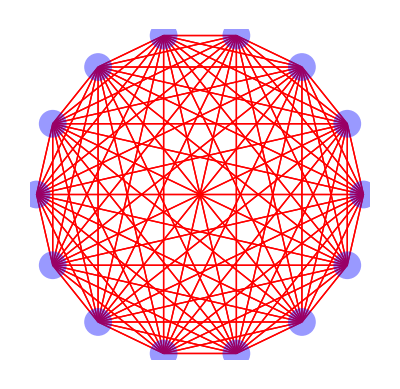

```mathematica
plotRegularPolygonWithAllDiagonals[14]
```

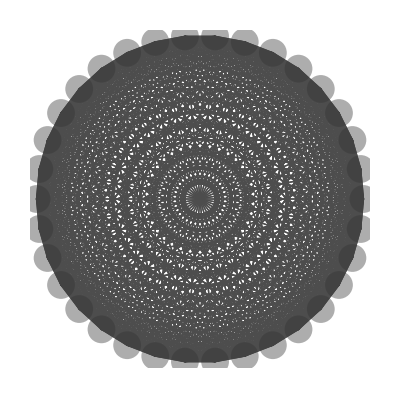

```mathematica
plotRegularPolygonWithAllDiagonals[34,"LineColor"->GrayLevel[0.3],"VertexColor"->GrayLevel[0.2]]
```

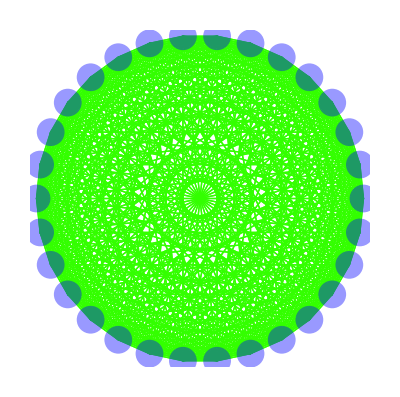

```mathematica
plotRegularPolygonWithAllDiagonals[30,"LineColor"->Hue[0.3]]
```

## Estructura de los Gráficos

### Estructura de Gráficos en 3D

#### Graphics3D

Graphics3D[prim]
Graphics3D[prim, opts]
Graphics3D[{dir1, dir2, prim}]
Graphics3D[{{dir11, dir12, ..., prim1}, {dir21, dir22, ..., prim2}, ...}]

#### Primitives

Point[p]              		  			Point at position p
Line[{p1,p2,...}]     		  			Line through points p1, p2, ...
Arrow[{p1,p2,...}]     		  			Arrow through points p1, p2, ...
Polygon[{p1,p2,...}]           				Polygon with vertices p1, p2, ...
Text[expr,p]                   				Text element centered at p

Cone[{{xa,ya,za},{xb,yb,zb}}] 				Unite Cone
Cone[{{xa,ya,za},{xb,yb,zb}},r] 				Cone with radius base r
Cuboid[{xa,ya,za}]    						Unit cube.
Cuboid[{xa,ya,za},{xb,yb,zb}]  				Rectangular parallelepiped
Cylinder[{{xa,ya,za},{xb,yb,zb}}]				Cylinder of radius 1
Cylinder[{{xa,ya,za},{xb,yb,zb}},r]				Cylinder of radius r
Sphere[{xa,ya,za}] 						Sphere of radius 1
Sphere[{xa,ya,za},r] 						Sphere of radius r
Tube[{{xa,ya,za},{xb,yb,zb},...}]				Tube of radius 1
Tube[{{xa,ya,za},{xb,yb,zb},...},r]				Tube of radius r
Raster3D[array]

#### Attributes (Directives)

PointSize[r],							
AbsolutePointSize[r]
r = Small, Large

Thickness[r],						
AbsoluteThickness[r]
Thick

Dashing[{r1,r2,...}],			
AbsoluteDashing[{r1,r2,...}]
Dashed, Dotted

EdgeForm[g]
FaceForm[g]
CapForm[type]
JoinForm[type]

Opacity[a]					opacity a
GrayLevel[g] 					Gray g
RGBColor[r,g,b]				Color with r,g,b componentes
Hue[h] 						Hue hue
Hue[h,s,b]					Hue hue,saturation,brightness

Directive[g1,g2,...]

#### Point

```mathematica
data=Table[{t,Sin[t],Cos[t]},{t,0,6π,2π/10}];
```

```mathematica
Graphics3D[{Blue,PointSize[0.01],Point[data]}]
```

#### Line

```mathematica
Graphics3D[Line[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}]]
```

```mathematica
l=Line[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}];
```

```mathematica
{Graphics3D[{Dashed,l}],Graphics3D[{Pink,l}],Graphics3D[{Thick,l}],Graphics3D[{Thick,Dashed,Pink,l}]}
```

#### Arrow

```mathematica
Graphics3D[Arrow[{{1,1,-1},{2,2,0},{3,3,-1},{4,4,0}}]]
```

```mathematica
Graphics3D[{Red,Arrowheads[0.1],Arrow[{{1,1,-1},{2,2,0},{3,3,-1},{4,4,0}}]}]
```

```mathematica
Graphics3D[{Red,Arrowheads[0.1],Arrow[Tube[{{1,1,-1},{2,2,0},{3,3,-1},{4,4,0}},0.05]]}]
```

```mathematica
{Graphics3D[
{Arrowheads[{-.1,.1}],Arrow[{{0,0,0},{2,1,1}}]}],
Graphics3D[{Arrowheads[{-.1,.1}],Arrow[Tube[{{0,0,0},{2,1,1}}]]}]}
```

#### Polygon

```mathematica
Graphics3D[{FaceForm[Orange,Blue],Polygon[{{1,0,0},{1,1,1},{0,0,1}}]},Lighting->"Neutral"]
```

```mathematica
p=Polygon[{{1,0,0},{1,1,1},{0,0,1}}];
```

```mathematica
{Graphics3D[{Pink,p}],Graphics3D[{EdgeForm[Thick],FaceForm[Opacity[0.7],Pink],p}],Graphics3D[{EdgeForm[Dashed],Pink,p}],Graphics3D[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,p}]}
```

```mathematica
Graphics3D[{FaceForm[Directive[Opacity[0.8],Orange],Directive[Opacity[0.8],Red]],Polygon[Table[{0,Cos[2n π/49],Sin[2 n π/49]},{n,0,50}]]},Lighting->"Neutral"]
```

#### Text

```mathematica
Graphics3D[{Sphere[],Text[x^2+y^2+z^2<1,{0,0,0}]}]
```

#### Raster3D

```mathematica
Graphics3D[{Raster3D[RandomReal[1,{5,5,5}]]}]
```

```mathematica
Graphics3D[{Opacity[.5],Raster3D[RandomReal[1,{3,3,3,3}]]},Boxed->False]
```

#### Cone

```mathematica
Graphics3D[Cone[{{0,0,0},{1,1,1}},1/2]]
```

```mathematica
{Graphics3D[{Yellow,Cone[]}],Graphics3D[{EdgeForm[Thick],Cone[]}],Graphics3D[{EdgeForm[Dashed],Cone[]}],Graphics3D[{EdgeForm[Directive[Thick,Dashed,Blue]],Orange,Cone[]}]}
```

#### Cuboid

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0}],Blue,Cuboid[{0.5,0.5,0.5}]}]
```

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0},{1,3,1}],Blue,Cuboid[{2,1,1},{4,2,3}]}]
```

```mathematica
{Graphics3D[{Pink,Cuboid[]}],Graphics3D[{EdgeForm[Thick],Cuboid[]}],Graphics3D[{EdgeForm[Dashed],Cuboid[]}],Graphics3D[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Cuboid[]}]}
```

#### Cylinder

```mathematica
Graphics3D[Cylinder[{{0,0,0},{1,1,1}},1/2]]
```

```mathematica
{Graphics3D[{Yellow,Cylinder[]}],Graphics3D[{EdgeForm[Thick],Cylinder[]}],Graphics3D[{EdgeForm[Dashed],Cylinder[]}],Graphics3D[{EdgeForm[Directive[Thick,Dashed,Blue]],Yellow,Cylinder[]}]}
```

#### Sphere

```mathematica
Graphics3D[{Sphere[{0,0,0},1],Sphere[{5,5,5},1]}]
```

```mathematica
Graphics3D[{FaceForm[Yellow,Blue],Sphere[]},PlotRange->{{-1,1},{-.8,1},{-1,1}}]
```

```mathematica
Table[Graphics3D[{Orange,Specularity[White,n],Sphere[]}],{n,{5,20,100}}]
```

#### Tube

```mathematica
Graphics3D[Tube[{{0,0,0},{1,1,1}},.1]]
```

```mathematica
t=Tube[{{-1,-1,-1},{0,0,1},{1,1,-1}},0.4];
```

```mathematica
{Graphics3D[{Red,t}],Graphics3D[{CapForm["Round"],t}],Graphics3D[{JoinForm["Miter"],t}]}
```

#### Ejemplo

```mathematica
g=Plot3D[Sin[x y],{x,0,2},{y,0,2},Axes->False,Boxed->False,Mesh->None,PlotPoints->3,MaxRecursion->0]
```

```mathematica
g//FullForm
```

```mathematica
Head[g]
```

```mathematica
First[g]
```

#### Ejemplo

```mathematica
Graphics3D[{
Blue,Cylinder[],
Red,Sphere[{0,0,2}],
Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],
Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},
{3,3,-2},{3,-3,-2}}],
Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

#### Ejemplo

```mathematica
rcoord:=RandomReal[1.,{3}]
pts={Red,AbsolutePointSize[10],Table[Point[rcoord],{20}]};
rantri:={Opacity[0.5],Hue[Random[]],Polygon[Table[rcoord,{3}]]}
```

```mathematica
Graphics3D[{
pts,
{Blue,Thickness[0.01],Line[Table[rcoord,{10}]]},
Table[rantri,{10}]},Boxed->False]
```

-Graphics3D-

```mathematica
%85/.Point[x_]:>{Hue[Random[]],Sphere[x,0.05]}
```

%85

## Programación Gráfica

### Caminos Cerrados Simples

```mathematica
coords=RandomReal[1,{10,2}]
```

{{0.561845,0.12265},{0.597645,0.373021},{0.641292,0.809334},{0.24153,0.722588},{0.550651,0.439533},{0.148846,0.041673},{0.664948,0.579257},{0.126971,0.242237},{0.977633,0.0704797},{0.343446,0.80822}}

```mathematica
points=Point[coords]
```

Point[{{0.561845,0.12265},{0.597645,0.373021},{0.641292,0.809334},{0.24153,0.722588},{0.550651,0.439533},{0.148846,0.041673},{0.664948,0.579257},{0.126971,0.242237},{0.977633,0.0704797},{0.343446,0.80822}}]

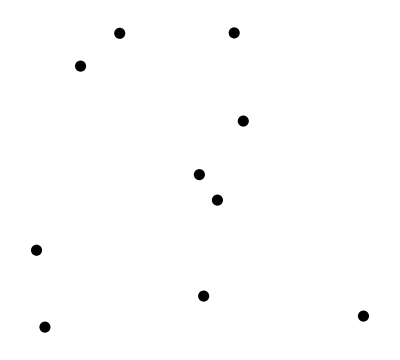

```mathematica
Graphics[{PointSize[0.02],points}]
```

```mathematica
lines=Line[coords]
```

Line[{{0.561845,0.12265},{0.597645,0.373021},{0.641292,0.809334},{0.24153,0.722588},{0.550651,0.439533},{0.148846,0.041673},{0.664948,0.579257},{0.126971,0.242237},{0.977633,0.0704797},{0.343446,0.80822}}]

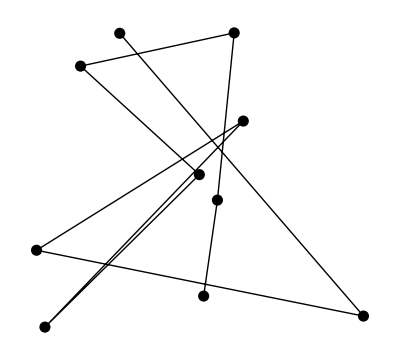

```mathematica
Graphics[{PointSize[0.02],points,lines}]
```

```mathematica
PointJoinedPlot[coords_]:=Graphics[{
Hue[0.],Line[coords],
Hue[0.6],PointSize[0.02],Point[coords]}]
```

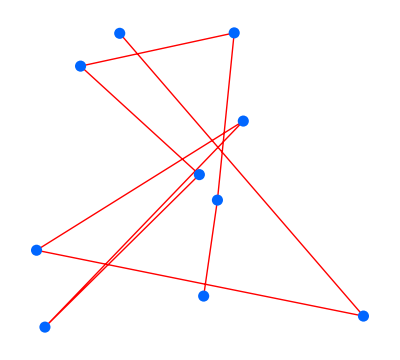

```mathematica
PointJoinedPlot[coords]
```

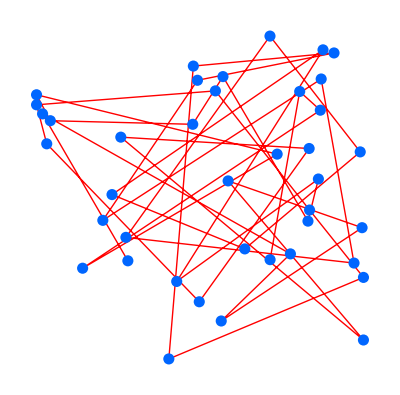

```mathematica
PointJoinedPlot[RandomReal[1,{40,2}]]
```

```mathematica
path=Join[coords,{First[coords]}]
```

{{0.561845,0.12265},{0.597645,0.373021},{0.641292,0.809334},{0.24153,0.722588},{0.550651,0.439533},{0.148846,0.041673},{0.664948,0.579257},{0.126971,0.242237},{0.977633,0.0704797},{0.343446,0.80822},{0.561845,0.12265}}

```mathematica
PointJoinedPlot[path]
```

-Graphics-

```mathematica
base=Flatten[Select[coords,#[[2]]==Min[coords[[All,2]]]&]]
```

{0.148846,0.041673}

```mathematica
angle[a_List,b_List]:=ArcTan@@(b-a)
```

```mathematica
remain=Complement[coords,{base}]
```

```mathematica
angle[base,#]&/@remain
```

```mathematica
s=Sort[remain,angle[base,#1]≤angle[base,#2]&]
```

```mathematica
path=Join[{base},s,{base}]
```

```mathematica
PointJoinedPlot[path]
```

```mathematica
simpleClosedPath[lista_]:=
Module[{base,angle,sorted},

base=Flatten[Select[lista,
#[[2]]==Min[lista[[All,2]]]&]];

angle[a_List,b_List]:=ArcTan@@(b-a);

sorted=Sort[Complement[lista,{base}],angle[base,#1]≤angle[base,#2]&];

Join[{base},sorted,{base}]
]
```

```mathematica
puntos=RandomReal[1,{RandomInteger[{3,30}],2}]
```

```mathematica
simpleClosedPath[puntos]
```

```mathematica
PointJoinedPlot[%]
```

```mathematica
GraphicsGrid[Table[PointJoinedPlot[simpleClosedPath[RandomReal[1,{RandomInteger[{3,30}],2}]]],{10},{10}]]
```

## Programación Gráfica

### Gráfico de la Curva de Koch

```mathematica
basicProfile=N[{{0,0},{1/3,0},{1/2,(√3)/6},{2/3,0},{1,0}}]
```

{{0.,0.},{0.333333,0.},{0.5,0.288675},{0.666667,0.},{1.,0.}}

```mathematica
Graphics[Line[basicProfile]]
```

-Graphics-

La curva de Koch la obtenemos repitiendo esta construcción en cada segmento de la figura base. Luego, dado un segmento cualquiera, debemos escribir un algoritmo que rote la figura base en la dirección de este segmento y la escale al tamaño de este.

[]→

```mathematica
line={{1,1},{5,5}}
```

{{1,1},{5,5}}

```mathematica
Graphics[Line[line]]
```

-Graphics-

```mathematica
vector=Last[line]-First[line]
```

{4,4}

```mathematica
pointOfProfile={1,0}
```

{1,0}

```mathematica
rotationMatrix=N[RotationMatrix[{{1,0}, vector}]]
```

{{0.707107,-0.707107},{0.707107,0.707107}}

```mathematica
rotationMatrix.pointOfProfile
```

{0.707107,0.707107}

```mathematica
newPointOfProfile=First[line]+Norm[vector]rotationMatrix.pointOfProfile
```

{5.,5.}

```mathematica
newProfile=(First[line]+Norm[vector]rotationMatrix.#1&)/@basicProfile
```

{{1.,1.},{2.33333,2.33333},{1.8453,4.1547},{3.66667,3.66667},{5.,5.}}

```mathematica
Graphics[{Line@basicProfile,Line[newProfile]}]
```

-Graphics-

```mathematica
Clear[vector,rotationMatrix,line,pointOfProfile,newPointOfProfile]
```

```mathematica
nextProfile[{{x1_,y1_},{x2_,y2_}}]:=Module[{rotationMatrix,vector,basicProfile,newProfile,r},
vector={x2-x1,y2-y1};
r=Norm[vector];
rotationMatrix=N[Quiet[RotationMatrix[{{1,0}, vector}]]];
basicProfile=N[{{0,0},{1/3,0},{1/2,(√3)/6},{2/3,0},{1,0}}];newProfile=({x1,y1}+r rotationMatrix.#1&)/@basicProfile]
```

nextProfile tiene como argumento una lista que contiene los puntos inicial y final de cada segmento. Para aplicar esta función a cada segmento de la línea base, debemos construir a partir de la lista de sus vértices la lista correspondiente de los segmentos

```mathematica
nextProfile[{{0,0},{1/3,0}}]
```

{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.}}

```mathematica
Graphics[{Red,Line[{{0,0},{1/3,0}}],Blue,Line@nextProfile[{{0,0},{1/3,0}}]}]
```

-Graphics-

```mathematica
N[basicProfile]
```

{{0.,0.},{0.333333,0.},{0.5,0.288675},{0.666667,0.},{1.,0.}}

```mathematica
Partition[N[basicProfile],2,1]
```

{{{0.,0.},{0.333333,0.}},{{0.333333,0.},{0.5,0.288675}},{{0.5,0.288675},{0.666667,0.}},{{0.666667,0.},{1.,0.}}}

```mathematica
nextProfile/@Partition[basicProfile,2,1]
```

{{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.}},{{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675}},{{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.}},{{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}}

```mathematica
Flatten[Rest/@%,1]
```

{{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}

```mathematica
First[First[%%]]
```

{0.,0.}

```mathematica
Prepend[Flatten[Rest/@#,1],First[First[#]]]&[nextProfile/@Partition[basicProfile,2,1]]
```

{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}

```mathematica
%//Line//Graphics
```

-Graphics-

```mathematica
lineSequence[lis_]:=Prepend[Flatten[Rest/@#,1],First[First[#]]]&[lis]
```

```mathematica
lineSequence[nextProfile/@Partition[basicProfile,2,1]]//Line//Graphics
```

-Graphics-

```mathematica
kochCurve[pointsList_List,n_Integer]:=Nest[lineSequence[nextProfile/@Partition[#1,2,1]]&,pointsList,n]
```

```mathematica
kochCurve[{{0,0},{1,0}},4];
```

```mathematica
%//Line//Graphics
```

-Graphics-

```mathematica
Clear[nextProfile,lineSequence,kochCurve]
```

```mathematica
ClearAll[kochCurve];
Options[kochCurve]=
{"BasicProfile"->N[{{0,0},{1/3,0},{1/2,(√3)/6},{2/3,0},{1,0}}]};

kochCurve[pointsList_List,n_Integer,OptionsPattern[]]:=
Module[
{nextProfile,lineSequence},

nextProfile[{{x1_,y1_},{x2_,y2_}}]:=Module[{rotationMatrix,vector,basicProfile,newProfile,r, profileBaseVector},
vector={x2-x1,y2-y1};
r=Norm[vector];
basicProfile=OptionValue["BasicProfile"];
profileBaseVector=Last[basicProfile]-First[basicProfile];

rotationMatrix=N[Quiet[RotationMatrix[{profileBaseVector, vector}]]];
newProfile=({x1,y1}+r/Norm[profileBaseVector] rotationMatrix.#1&)/@basicProfile];

lineSequence[lis_]:=Prepend[Flatten[Rest/@#,1],First[First[#]]]&[lis];

Nest[lineSequence[nextProfile/@Partition[#1,2,1]]&,pointsList,n]

]
```

```mathematica
RotationMatrix[{{0,1}, {-2,0}}]
```

{{0,-1},{1,0}}

```mathematica
PlotKochCurve[list_List,n_Integer]:=Graphics[Line[kochCurve[list,n]],AspectRatio->Automatic]
```

```mathematica
PlotKochCurve[{{0,0},{1,0}},5]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,1}},5]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1/2,(√3)/2},{1,0},{0,0}},5]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{0,1},{1,1},{1,0},{0,0}},4]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,0},{1,1},{0,1},{0,0}},5]
```

-Graphics-

```mathematica
Clear[PlotKochCurve];

PlotKochCurve[list_List,n_Integer,col:_?ColorQ:Red,opts___Rule]:=Graphics[{col,Line[kochCurve[list,n]]},opts,AspectRatio->Automatic]
```

```mathematica
PlotKochCurve[{{0,0},{1,0}},4,GrayLevel[0.4],AspectRatio->0.5,Frame->True,FrameTicks->Automatic]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,0}},4,AspectRatio->0.5,Frame->True,FrameTicks->None]
```

-Graphics-

```mathematica
Clear[PlotKochCurve];

Options[PlotKochCurve]=Join[
{"KochCurveStyle"->{Red},
"BasicProfile"->N[{{0,0},{1/3,0},{1/2,(√3)/6},{2/3,0},{1,0}}]},
Options[Graphics]];

PlotKochCurve[list_List,n_Integer,opts:OptionsPattern[]]:=Graphics[{Sequence@@OptionValue["KochCurveStyle"],Line[kochCurve[list,n,"BasicProfile"->OptionValue["BasicProfile"]]]},
Sequence@@FilterRules[{opts},Options[Graphics]],AspectRatio->Automatic]
```

```mathematica
PlotKochCurve[{{0,0},{1,0}},4]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,0}},5,AspectRatio->0.3,Frame->True,ImageSize->700,FrameTicks->None,"KochCurveStyle"->{Blue}]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,0},{1,1},{0,1},{0,0}},5,AspectRatio->Automatic,Frame->True,ImageSize->500,FrameTicks->None,
"KochCurveStyle"->{Blue},"BasicProfile"->10N[{{0,0},{1/3,0},{1/2,(√3)/6},{2/3,0},{1,0}}]]
```

-Graphics-

```mathematica
PlotKochCurve[{{0,0},{1,0}},4,AspectRatio->Automatic,Frame->True,FrameStyle->Orange,ImageSize->500,FrameTicks->None,
"KochCurveStyle"->{Blue},"BasicProfile"->{{0,0},{1/4,0},{1/4,1/4},{2/4,1/4},{2/4,0},{2/4,-1/4},{3/4,-1/4},{3/4,0},{1,0}}]
```

-Graphics-

## Programación Gráfica

### Gráfico de Raices de una Función

```mathematica
sinplot=Plot[Sin[2x],{x,-1,7}]
```

-Graphics-

```mathematica
pts=Cases[sinplot,Line[{x__}]->x,∞];
```

```mathematica
Split[pts,Sign[Last[#2]]==-Sign[Last[#1]]&];
```

```mathematica
Select[%,Length[#1]==2&]
```

{{{-0.031127,-0.0622139},{0.139847,0.276061}},{{1.44436,0.250178},{1.61176,-0.0818453}},{{3.07602,-0.130778},{3.24489,0.205125}},{{4.70606,0.0126532},{4.87641,-0.322185}},{{6.18406,-0.196957},{6.34267,0.118683}}}

```mathematica
Map[First,%,{2}]
```

{{-0.031127,0.139847},{1.44436,1.61176},{3.07602,3.24489},{4.70606,4.87641},{6.18406,6.34267}}

```mathematica
FindRoot[Sin[2x]==0,{x,#[[1]],#[[2]]}]&/@%
```

{{x→-3.75498×10^-28},{x→1.5708},{x→3.14159},{x→4.71239},{x→6.28319}}

```mathematica
roots=If[Length[%]>1,x/.%,{}]
```

{-3.75498×10^-28,1.5708,3.14159,4.71239,6.28319}

```mathematica
pts=Tooltip[Point[{#,0}],NumberForm[#//Chop,{8,3}]]&/@roots
```

{Point[{-3.75498×10^-28,0}],Point[{1.5708,0}],Point[{3.14159,0}],Point[{4.71239,0}],Point[{6.28319,0}]}

```mathematica
Show[sinplot,
Graphics[{RGBColor[1,0,0],PointSize[0.02],pts}]]
```

-Graphics-

```mathematica
Attributes[Plot]
```

{HoldAll,Protected,ReadProtected}

```mathematica
Clear[RootPlot];

Options[RootPlot]=Join[{"RootDotStyle"->{RGBColor[1,0,0],PointSize[0.02]}},Options[Plot]];

RootPlot[fun_,{x_,xmin_,xmax_},opts:OptionsPattern[]]:=
Module[{fplot,pts,z,spts,roots,points},

fplot=Plot[fun,{x,xmin,xmax},Evaluate[Sequence@@FilterRules[{opts},Options[Plot]]]];

pts=Cases[fplot,Line[{z__}]->z,∞];

spts=Map[First,Select[Split[pts,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];

roots=FindRoot[fun==0,{x,#[[1]],#[[2]]}]&/@spts;

points=Tooltip[Point[{#,0}],NumberForm[#//Chop,{8,3}]]&/@If[Length[roots]>1,x/.roots,{}];

Show[fplot,
Graphics[{Sequence@@OptionValue["RootDotStyle"],points}]]
]
```

```mathematica
RootPlot[Sin[x+√2 Sin[x]],{x,-π,3π}]
```

-Graphics-

```mathematica
RootPlot[Re[1/2+Zeta[ⅈ t]],{t,20,40}]
```

-Graphics-

```mathematica
RootPlot[Sin[x+√2 Sin[x]],{x,-π,3π},"RootDotStyle"->{PointSize[0.03],Opacity[0.4],Blue},Frame->True,PlotStyle->Orange,Axes->{True,None}]
```

-Graphics-

## Programación Gráfica

### Graficando Árboles

```mathematica
Graphics[Line[{{0,0},{1,1}}],AspectRatio->Automatic]
```

-Graphics-

```mathematica
rotation=0.3;
shrinkage=0.8;
```

```mathematica
twinLine[Line[{start_,end_}]]:={Line[{end,end+shrinkage RotationTransform[rotation,{0,0}][end-start]}],Line[{end,end+shrinkage RotationTransform[-rotation,{0,0}][end-start]}]}
```

```mathematica
twinLine[Line[{{0,0},{1,1}}]]
```

{Line[{{1,1},{1.52785,2.00069}}],Line[{{1,1},{2.00069,1.52785}}]}

```mathematica
Graphics[{Line[{{0,0},{1,1}}],twinLine[Line[{{0,0},{1,1}}]]},AspectRatio->Automatic]
```

-Graphics-

```mathematica
doTwins[lines_]:=Flatten[twinLine/@lines]
```

```mathematica
doTwins[{Line[{{0,0},{0,1}}]}]
```

{Line[{{0,1},{-0.236416,1.76427}}],Line[{{0,1},{0.236416,1.76427}}]}

```mathematica
doTwins[%]
```

{Line[{{-0.236416,1.76427},{-0.597787,2.29248}}],Line[{{-0.236416,1.76427},{-0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.597787,2.29248}}]}

```mathematica
Graphics[%]
```

-Graphics-

```mathematica
Nest[doTwins,{Line[{{0,0},{0,1}}]},2]
```

{Line[{{-0.236416,1.76427},{-0.597787,2.29248}}],Line[{{-0.236416,1.76427},{-0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.597787,2.29248}}]}

```mathematica
Graphics[%]
```

-Graphics-

```mathematica
NestList[doTwins,{Line[{{0,0},{0,1}}]},3]
```

{{Line[{{0,0},{0,1}}]},{Line[{{0,1},{-0.236416,1.76427}}],Line[{{0,1},{0.236416,1.76427}}]},{Line[{{-0.236416,1.76427},{-0.597787,2.29248}}],Line[{{-0.236416,1.76427},{-0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.236416,2.40427}}],Line[{{0.236416,1.76427},{0.597787,2.29248}}]},{Line[{{-0.597787,2.29248},{-0.998851,2.61075}}],Line[{{-0.597787,2.29248},{-0.749094,2.78162}}],Line[{{-0.236416,2.40427},{-0.387723,2.8934}}],Line[{{-0.236416,2.40427},{-0.0851098,2.8934}}],Line[{{0.236416,2.40427},{0.0851098,2.8934}}],Line[{{0.236416,2.40427},{0.387723,2.8934}}],Line[{{0.597787,2.29248},{0.749094,2.78162}}],Line[{{0.597787,2.29248},{0.998851,2.61075}}]}}

```mathematica
Graphics[NestList[doTwins,{Line[{{0,0},{0,1}}]},3],AspectRatio->Automatic,PlotRange->All]
```

-Graphics-

```mathematica
tree[nestingDepth_,rotationP_,shrinkageP_,options___]:=Block[{rotation=rotationP,shrinkage=shrinkageP},Graphics[NestList[doTwins,{Line[{{0,0},{0,1}}]},nestingDepth],options,AspectRatio->Automatic,PlotRange->All]]
```

```mathematica
tree[3,0.2,0.8,AspectRatio->1]
```

-Graphics-

```mathematica
tree[7,0.3,0.8]
```

-Graphics-

```mathematica
tree[8,0.5,0.8,BaseStyle->Brown]
```

-Graphics-

```mathematica
thicknessShrinkage = 0.8;
originalThickness = 0.05;
```

```mathematica
twinLine[Thickness[th_]]:=Thickness[th thicknessShrinkage];
```

```mathematica
Clear[tree];
tree[nestingDepth_,rotationP_,shrinkageP_,thicknessShrinkageP_,originalThicknessP_,options___]:=Block[{rotation=rotationP,shrinkage=shrinkageP,thicknessShrinkage=thicknessShrinkageP,originalThickness=originalThicknessP},Graphics[NestList[doTwins,{Thickness[originalThickness],Line[{{0,0},{0,1}}]},nestingDepth],options,AspectRatio->Automatic,PlotRange->All]]
```

```mathematica
tree[6,0.3,0.8,0.7,0.05]
```

-Graphics-

```mathematica
tree[8,0.5,0.8,0.75,0.05,BaseStyle->Brown]
```

-Graphics-

```mathematica
Clear[rotateLine,twinLine,doTwins];

rotateLine[Line[{start_,end_}],angle_]:=Line[{end,end+branchShortening RotationTransform[-angle Random[Real,{0.5,1.5}],{0,0}][end-start]}];

twinLine[Line[points_]]:={rotateLine[Line[points],branchRotation],rotateLine[Line[points],-branchRotation]};
twinLine[Thickness[th_]]:=Thickness[th branchThinning];
twinLine[RGBColor[r_,g_,b_]]:=(branchColors=RotateLeft[branchColors];First[branchColors]);

doTwins[lines_]:=Flatten[twinLine/@lines];

Options[BeautifulTree]=Join[{Generations->10,BranchRotation->0.65,BranchShortening->0.750,BranchThinning->0.7,OriginalThickness->0.070,BranchColors->{RGBColor[0.562,0.236,0.071],RGBColor[0.547,0.229,0.069],RGBColor[0.500,0.210,0.063],RGBColor[0.469,0.196,0.059],RGBColor[0.033,0.281,0.035],RGBColor[0.046,0.395,0.050],RGBColor[0.055,0.469,0.059],RGBColor[0.070,0.602,0.076],RGBColor[0.085,0.727,0.092],RGBColor[0.109,0.937,0.118],RGBColor[0.013,0.750,0.028]}},Options[Graphics]];

BeautifulTree[options:OptionsPattern[]]:=Block[{generations,branchRotation,branchShortening,branchThinning,originalThickness,branchColors},{generations,branchRotation,branchShortening,branchThinning,originalThickness,branchColors}=OptionValue[#]&/@{Generations,BranchRotation,BranchShortening,BranchThinning,OriginalThickness,BranchColors};Graphics[NestList[doTwins,{First[branchColors],Thickness[originalThickness],Line[{{0,0},{0,1}}]},generations],Sequence@@FilterRules[{options},Options[Graphics]],AspectRatio->Automatic,PlotRange->All,BaseStyle->GrayLevel[0.8]]];
```

```mathematica
BeautifulTree[]
```

-Graphics-

```mathematica
BeautifulTree[Frame->True,FrameTicks->False,PlotRangePadding->1,BaseStyle->Hue[0]]
```

-Graphics-

```mathematica
BeautifulTree[Generations->10,BranchRotation->0.5]
```

-Graphics-

```mathematica
BeautifulTree[Generations->10,BranchRotation->0.65,BranchShortening->0.75,BranchThinning->0.7,OriginalThickness->0.07]
```

-Graphics-

```mathematica
BeautifulTree[BranchColors->{RGBColor[0.562,0.236,0.071],RGBColor[0.547,0.229,0.069],RGBColor[0.500,0.210,0.063],RGBColor[0.469,0.196,0.059],RGBColor[0.033,0.281,0.035],RGBColor[0.046,0.395,0.050],RGBColor[0.055,0.469,0.059],RGBColor[0.070,0.602,0.076],RGBColor[0.085,0.727,0.092],RGBColor[0.109,0.937,0.118],RGBColor[0.013,0.750,0.028]}]
```

-Graphics-

```mathematica
BeautifulTree[BranchColors->{RGBColor[0.562,0.236,0.071],RGBColor[0.547,0.229,0.069],RGBColor[0.500,0.210,0.063],RGBColor[0.469,0.196,0.059],RGBColor[0.033,0.281,0.035],RGBColor[0.562,0.154,0.084],RGBColor[0.750,0.206,0.112],RGBColor[0.875,0.240,0.131],RGBColor[0.902,0.248,0.135],RGBColor[0.902,0.160,0.125],RGBColor[0.977,0.048,0.039]}]
```

-Graphics-